```mathematica
(*Equation of motion?*)
M=Flatten[Table[D[Subscript[ρ, n,m][t],t]==-I (Subscript[w, En][n,m])Subscript[ρ, n,m]+I/ℏ Sum[Subscript[d, n,v] Ε[n,v] Subscript[ρ, v,m]-Subscript[ρ, n,v] Subscript[d, v,m] Ε[v,m],{v,1,4}]+If[n≠m,-Subscript[γ, n,m] Subscript[ρ, n,m],Sum[If[n≥ 3,-Γ[v,n] Subscript[ρ, n,n],Γ[n,v] Subscript[ρ, v,v]],{v,1,4}]],{n,1,4},{m,1,4}]//Expand,1];
%//TableForm
```

ρ_(1,1)'[t]==ⅈ ρ_(1,1) w[1,1]+ρ_(1,1) Γ[1,1]+ρ_(2,2) Γ[1,2]+ρ_(3,3) Γ[1,3]+ρ_(4,4) Γ[1,4]+(ⅈ d_(1,2) ρ_(2,1) Ε[1,2])/ℏ+(ⅈ d_(1,3) ρ_(3,1) Ε[1,3])/ℏ+(ⅈ d_(1,4) ρ_(4,1) Ε[1,4])/ℏ-(ⅈ d_(2,1) ρ_(1,2) Ε[2,1])/ℏ-(ⅈ d_(3,1) ρ_(1,3) Ε[3,1])/ℏ-(ⅈ d_(4,1) ρ_(1,4) Ε[4,1])/ℏ
ρ_(1,2)'[t]==-γ_(1,2) ρ_(1,2)+ⅈ ρ_(1,2) w[2,1]+(ⅈ d_(1,1) ρ_(1,2) Ε[1,1])/ℏ-(ⅈ d_(1,2) ρ_(1,1) Ε[1,2])/ℏ+(ⅈ d_(1,2) ρ_(2,2) Ε[1,2])/ℏ+(ⅈ d_(1,3) ρ_(3,2) Ε[1,3])/ℏ+(ⅈ d_(1,4) ρ_(4,2) Ε[1,4])/ℏ-(ⅈ d_(2,2) ρ_(1,2) Ε[2,2])/ℏ-(ⅈ d_(3,2) ρ_(1,3) Ε[3,2])/ℏ-(ⅈ d_(4,2) ρ_(1,4) Ε[4,2])/ℏ
ρ_(1,3)'[t]==-γ_(1,3) ρ_(1,3)+ⅈ ρ_(1,3) w[3,1]+(ⅈ d_(1,1) ρ_(1,3) Ε[1,1])/ℏ+(ⅈ d_(1,2) ρ_(2,3) Ε[1,2])/ℏ-(ⅈ d_(1,3) ρ_(1,1) Ε[1,3])/ℏ+(ⅈ d_(1,3) ρ_(3,3) Ε[1,3])/ℏ+(ⅈ d_(1,4) ρ_(4,3) Ε[1,4])/ℏ-(ⅈ d_(2,3) ρ_(1,2) Ε[2,3])/ℏ-(ⅈ d_(3,3) ρ_(1,3) Ε[3,3])/ℏ-(ⅈ d_(4,3) ρ_(1,4) Ε[4,3])/ℏ
ρ_(1,4)'[t]==-γ_(1,4) ρ_(1,4)+ⅈ ρ_(1,4) w[4,1]+(ⅈ d_(1,1) ρ_(1,4) Ε[1,1])/ℏ+(ⅈ d_(1,2) ρ_(2,4) Ε[1,2])/ℏ+(ⅈ d_(1,3) ρ_(3,4) Ε[1,3])/ℏ-(ⅈ d_(1,4) ρ_(1,1) Ε[1,4])/ℏ+(ⅈ d_(1,4) ρ_(4,4) Ε[1,4])/ℏ-(ⅈ d_(2,4) ρ_(1,2) Ε[2,4])/ℏ-(ⅈ d_(3,4) ρ_(1,3) Ε[3,4])/ℏ-(ⅈ d_(4,4) ρ_(1,4) Ε[4,4])/ℏ
ρ_(2,1)'[t]==-γ_(2,1) ρ_(2,1)-ⅈ ρ_(2,1) w[2,1]-(ⅈ d_(1,1) ρ_(2,1) Ε[1,1])/ℏ+(ⅈ d_(2,1) ρ_(1,1) Ε[2,1])/ℏ-(ⅈ d_(2,1) ρ_(2,2) Ε[2,1])/ℏ+(ⅈ d_(2,2) ρ_(2,1) Ε[2,2])/ℏ+(ⅈ d_(2,3) ρ_(3,1) Ε[2,3])/ℏ+(ⅈ d_(2,4) ρ_(4,1) Ε[2,4])/ℏ-(ⅈ d_(3,1) ρ_(2,3) Ε[3,1])/ℏ-(ⅈ d_(4,1) ρ_(2,4) Ε[4,1])/ℏ
ρ_(2,2)'[t]==ⅈ ρ_(2,2) w[2,2]+ρ_(1,1) Γ[2,1]+ρ_(2,2) Γ[2,2]+ρ_(3,3) Γ[2,3]+ρ_(4,4) Γ[2,4]-(ⅈ d_(1,2) ρ_(2,1) Ε[1,2])/ℏ+(ⅈ d_(2,1) ρ_(1,2) Ε[2,1])/ℏ+(ⅈ d_(2,3) ρ_(3,2) Ε[2,3])/ℏ+(ⅈ d_(2,4) ρ_(4,2) Ε[2,4])/ℏ-(ⅈ d_(3,2) ρ_(2,3) Ε[3,2])/ℏ-(ⅈ d_(4,2) ρ_(2,4) Ε[4,2])/ℏ
ρ_(2,3)'[t]==-γ_(2,3) ρ_(2,3)+ⅈ ρ_(2,3) w[3,2]-(ⅈ d_(1,3) ρ_(2,1) Ε[1,3])/ℏ+(ⅈ d_(2,1) ρ_(1,3) Ε[2,1])/ℏ+(ⅈ d_(2,2) ρ_(2,3) Ε[2,2])/ℏ-(ⅈ d_(2,3) ρ_(2,2) Ε[2,3])/ℏ+(ⅈ d_(2,3) ρ_(3,3) Ε[2,3])/ℏ+(ⅈ d_(2,4) ρ_(4,3) Ε[2,4])/ℏ-(ⅈ d_(3,3) ρ_(2,3) Ε[3,3])/ℏ-(ⅈ d_(4,3) ρ_(2,4) Ε[4,3])/ℏ
ρ_(2,4)'[t]==-γ_(2,4) ρ_(2,4)+ⅈ ρ_(2,4) w[4,2]-(ⅈ d_(1,4) ρ_(2,1) Ε[1,4])/ℏ+(ⅈ d_(2,1) ρ_(1,4) Ε[2,1])/ℏ+(ⅈ d_(2,2) ρ_(2,4) Ε[2,2])/ℏ+(ⅈ d_(2,3) ρ_(3,4) Ε[2,3])/ℏ-(ⅈ d_(2,4) ρ_(2,2) Ε[2,4])/ℏ+(ⅈ d_(2,4) ρ_(4,4) Ε[2,4])/ℏ-(ⅈ d_(3,4) ρ_(2,3) Ε[3,4])/ℏ-(ⅈ d_(4,4) ρ_(2,4) Ε[4,4])/ℏ
ρ_(3,1)'[t]==-γ_(3,1) ρ_(3,1)-ⅈ ρ_(3,1) w[3,1]-(ⅈ d_(1,1) ρ_(3,1) Ε[1,1])/ℏ-(ⅈ d_(2,1) ρ_(3,2) Ε[2,1])/ℏ+(ⅈ d_(3,1) ρ_(1,1) Ε[3,1])/ℏ-(ⅈ d_(3,1) ρ_(3,3) Ε[3,1])/ℏ+(ⅈ d_(3,2) ρ_(2,1) Ε[3,2])/ℏ+(ⅈ d_(3,3) ρ_(3,1) Ε[3,3])/ℏ+(ⅈ d_(3,4) ρ_(4,1) Ε[3,4])/ℏ-(ⅈ d_(4,1) ρ_(3,4) Ε[4,1])/ℏ
ρ_(3,2)'[t]==-γ_(3,2) ρ_(3,2)-ⅈ ρ_(3,2) w[3,2]-(ⅈ d_(1,2) ρ_(3,1) Ε[1,2])/ℏ-(ⅈ d_(2,2) ρ_(3,2) Ε[2,2])/ℏ+(ⅈ d_(3,1) ρ_(1,2) Ε[3,1])/ℏ+(ⅈ d_(3,2) ρ_(2,2) Ε[3,2])/ℏ-(ⅈ d_(3,2) ρ_(3,3) Ε[3,2])/ℏ+(ⅈ d_(3,3) ρ_(3,2) Ε[3,3])/ℏ+(ⅈ d_(3,4) ρ_(4,2) Ε[3,4])/ℏ-(ⅈ d_(4,2) ρ_(3,4) Ε[4,2])/ℏ
ρ_(3,3)'[t]==ⅈ ρ_(3,3) w[3,3]-ρ_(3,3) Γ[1,3]-ρ_(3,3) Γ[2,3]-ρ_(3,3) Γ[3,3]-ρ_(3,3) Γ[4,3]-(ⅈ d_(1,3) ρ_(3,1) Ε[1,3])/ℏ-(ⅈ d_(2,3) ρ_(3,2) Ε[2,3])/ℏ+(ⅈ d_(3,1) ρ_(1,3) Ε[3,1])/ℏ+(ⅈ d_(3,2) ρ_(2,3) Ε[3,2])/ℏ+(ⅈ d_(3,4) ρ_(4,3) Ε[3,4])/ℏ-(ⅈ d_(4,3) ρ_(3,4) Ε[4,3])/ℏ
ρ_(3,4)'[t]==-γ_(3,4) ρ_(3,4)+ⅈ ρ_(3,4) w[4,3]-(ⅈ d_(1,4) ρ_(3,1) Ε[1,4])/ℏ-(ⅈ d_(2,4) ρ_(3,2) Ε[2,4])/ℏ+(ⅈ d_(3,1) ρ_(1,4) Ε[3,1])/ℏ+(ⅈ d_(3,2) ρ_(2,4) Ε[3,2])/ℏ+(ⅈ d_(3,3) ρ_(3,4) Ε[3,3])/ℏ-(ⅈ d_(3,4) ρ_(3,3) Ε[3,4])/ℏ+(ⅈ d_(3,4) ρ_(4,4) Ε[3,4])/ℏ-(ⅈ d_(4,4) ρ_(3,4) Ε[4,4])/ℏ
ρ_(4,1)'[t]==-γ_(4,1) ρ_(4,1)-ⅈ ρ_(4,1) w[4,1]-(ⅈ d_(1,1) ρ_(4,1) Ε[1,1])/ℏ-(ⅈ d_(2,1) ρ_(4,2) Ε[2,1])/ℏ-(ⅈ d_(3,1) ρ_(4,3) Ε[3,1])/ℏ+(ⅈ d_(4,1) ρ_(1,1) Ε[4,1])/ℏ-(ⅈ d_(4,1) ρ_(4,4) Ε[4,1])/ℏ+(ⅈ d_(4,2) ρ_(2,1) Ε[4,2])/ℏ+(ⅈ d_(4,3) ρ_(3,1) Ε[4,3])/ℏ+(ⅈ d_(4,4) ρ_(4,1) Ε[4,4])/ℏ
ρ_(4,2)'[t]==-γ_(4,2) ρ_(4,2)-ⅈ ρ_(4,2) w[4,2]-(ⅈ d_(1,2) ρ_(4,1) Ε[1,2])/ℏ-(ⅈ d_(2,2) ρ_(4,2) Ε[2,2])/ℏ-(ⅈ d_(3,2) ρ_(4,3) Ε[3,2])/ℏ+(ⅈ d_(4,1) ρ_(1,2) Ε[4,1])/ℏ+(ⅈ d_(4,2) ρ_(2,2) Ε[4,2])/ℏ-(ⅈ d_(4,2) ρ_(4,4) Ε[4,2])/ℏ+(ⅈ d_(4,3) ρ_(3,2) Ε[4,3])/ℏ+(ⅈ d_(4,4) ρ_(4,2) Ε[4,4])/ℏ
ρ_(4,3)'[t]==-γ_(4,3) ρ_(4,3)-ⅈ ρ_(4,3) w[4,3]-(ⅈ d_(1,3) ρ_(4,1) Ε[1,3])/ℏ-(ⅈ d_(2,3) ρ_(4,2) Ε[2,3])/ℏ-(ⅈ d_(3,3) ρ_(4,3) Ε[3,3])/ℏ+(ⅈ d_(4,1) ρ_(1,3) Ε[4,1])/ℏ+(ⅈ d_(4,2) ρ_(2,3) Ε[4,2])/ℏ+(ⅈ d_(4,3) ρ_(3,3) Ε[4,3])/ℏ-(ⅈ d_(4,3) ρ_(4,4) Ε[4,3])/ℏ+(ⅈ d_(4,4) ρ_(4,3) Ε[4,4])/ℏ
ρ_(4,4)'[t]==ⅈ ρ_(4,4) w[4,4]-ρ_(4,4) Γ[1,4]-ρ_(4,4) Γ[2,4]-ρ_(4,4) Γ[3,4]-ρ_(4,4) Γ[4,4]-(ⅈ d_(1,4) ρ_(4,1) Ε[1,4])/ℏ-(ⅈ d_(2,4) ρ_(4,2) Ε[2,4])/ℏ-(ⅈ d_(3,4) ρ_(4,3) Ε[3,4])/ℏ+(ⅈ d_(4,1) ρ_(1,4) Ε[4,1])/ℏ+(ⅈ d_(4,2) ρ_(2,4) Ε[4,2])/ℏ+(ⅈ d_(4,3) ρ_(3,4) Ε[4,3])/ℏ

```mathematica
(*Applying Electric field is E Exp[-Iwt]*)
Subscript[w, En][n_,m_]:=If[n>m,w[n,m],-w[m,n]]
Subscript[w, Ex][i_,j_]:=If[i>j,Subscript[w, Ext][i,j],-Subscript[w, Ext][j,i]]
M1=M/.Flatten[Table[ Ε[i,j]->E0[i,j]Exp[-I Subscript[w, Ex][i,j]t],{i,1,4},{j,1,4}]];
%//TableForm
```

ρ_(1,1)'[t]==-(ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) E0[2,1] d_(2,1) ρ_(1,2))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) E0[3,1] d_(3,1) ρ_(1,3))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) E0[4,1] d_(4,1) ρ_(1,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[2,1]) E0[1,2] d_(1,2) ρ_(2,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,1]) E0[1,3] d_(1,3) ρ_(3,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,1]) E0[1,4] d_(1,4) ρ_(4,1))/ℏ+ⅈ ρ_(1,1) w[1,1]+ρ_(1,1) Γ[1,1]+ρ_(2,2) Γ[1,2]+ρ_(3,3) Γ[1,3]+ρ_(4,4) Γ[1,4]
ρ_(1,2)'[t]==-(ⅈ ⅇ^(ⅈ t w_Ext[2,1]) E0[1,2] d_(1,2) ρ_(1,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(1,2))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(1,2))/ℏ-γ_(1,2) ρ_(1,2)-(ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) E0[3,2] d_(3,2) ρ_(1,3))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) E0[4,2] d_(4,2) ρ_(1,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[2,1]) E0[1,2] d_(1,2) ρ_(2,2))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,1]) E0[1,3] d_(1,3) ρ_(3,2))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,1]) E0[1,4] d_(1,4) ρ_(4,2))/ℏ+ⅈ ρ_(1,2) w[2,1]
ρ_(1,3)'[t]==-(ⅈ ⅇ^(ⅈ t w_Ext[3,1]) E0[1,3] d_(1,3) ρ_(1,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,2]) E0[2,3] d_(2,3) ρ_(1,2))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(1,3))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(1,3))/ℏ-γ_(1,3) ρ_(1,3)-(ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) E0[4,3] d_(4,3) ρ_(1,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[2,1]) E0[1,2] d_(1,2) ρ_(2,3))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,1]) E0[1,3] d_(1,3) ρ_(3,3))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,1]) E0[1,4] d_(1,4) ρ_(4,3))/ℏ+ⅈ ρ_(1,3) w[3,1]
ρ_(1,4)'[t]==-(ⅈ ⅇ^(ⅈ t w_Ext[4,1]) E0[1,4] d_(1,4) ρ_(1,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,2]) E0[2,4] d_(2,4) ρ_(1,2))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,3]) E0[3,4] d_(3,4) ρ_(1,3))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(1,4))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(1,4))/ℏ-γ_(1,4) ρ_(1,4)+(ⅈ ⅇ^(ⅈ t w_Ext[2,1]) E0[1,2] d_(1,2) ρ_(2,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,1]) E0[1,3] d_(1,3) ρ_(3,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,1]) E0[1,4] d_(1,4) ρ_(4,4))/ℏ+ⅈ ρ_(1,4) w[4,1]
ρ_(2,1)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) E0[2,1] d_(2,1) ρ_(1,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(2,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(2,1))/ℏ-γ_(2,1) ρ_(2,1)-(ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) E0[2,1] d_(2,1) ρ_(2,2))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) E0[3,1] d_(3,1) ρ_(2,3))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) E0[4,1] d_(4,1) ρ_(2,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,2]) E0[2,3] d_(2,3) ρ_(3,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,2]) E0[2,4] d_(2,4) ρ_(4,1))/ℏ-ⅈ ρ_(2,1) w[2,1]
ρ_(2,2)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) E0[2,1] d_(2,1) ρ_(1,2))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[2,1]) E0[1,2] d_(1,2) ρ_(2,1))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) E0[3,2] d_(3,2) ρ_(2,3))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) E0[4,2] d_(4,2) ρ_(2,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,2]) E0[2,3] d_(2,3) ρ_(3,2))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,2]) E0[2,4] d_(2,4) ρ_(4,2))/ℏ+ⅈ ρ_(2,2) w[2,2]+ρ_(1,1) Γ[2,1]+ρ_(2,2) Γ[2,2]+ρ_(3,3) Γ[2,3]+ρ_(4,4) Γ[2,4]
ρ_(2,3)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) E0[2,1] d_(2,1) ρ_(1,3))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,1]) E0[1,3] d_(1,3) ρ_(2,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,2]) E0[2,3] d_(2,3) ρ_(2,2))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(2,3))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(2,3))/ℏ-γ_(2,3) ρ_(2,3)-(ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) E0[4,3] d_(4,3) ρ_(2,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,2]) E0[2,3] d_(2,3) ρ_(3,3))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,2]) E0[2,4] d_(2,4) ρ_(4,3))/ℏ+ⅈ ρ_(2,3) w[3,2]
ρ_(2,4)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) E0[2,1] d_(2,1) ρ_(1,4))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,1]) E0[1,4] d_(1,4) ρ_(2,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,2]) E0[2,4] d_(2,4) ρ_(2,2))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,3]) E0[3,4] d_(3,4) ρ_(2,3))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(2,4))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(2,4))/ℏ-γ_(2,4) ρ_(2,4)+(ⅈ ⅇ^(ⅈ t w_Ext[3,2]) E0[2,3] d_(2,3) ρ_(3,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,2]) E0[2,4] d_(2,4) ρ_(4,4))/ℏ+ⅈ ρ_(2,4) w[4,2]
ρ_(3,1)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) E0[3,1] d_(3,1) ρ_(1,1))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) E0[3,2] d_(3,2) ρ_(2,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(3,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(3,1))/ℏ-γ_(3,1) ρ_(3,1)-(ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) E0[2,1] d_(2,1) ρ_(3,2))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) E0[3,1] d_(3,1) ρ_(3,3))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) E0[4,1] d_(4,1) ρ_(3,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,3]) E0[3,4] d_(3,4) ρ_(4,1))/ℏ-ⅈ ρ_(3,1) w[3,1]
ρ_(3,2)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) E0[3,1] d_(3,1) ρ_(1,2))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) E0[3,2] d_(3,2) ρ_(2,2))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[2,1]) E0[1,2] d_(1,2) ρ_(3,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(3,2))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(3,2))/ℏ-γ_(3,2) ρ_(3,2)-(ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) E0[3,2] d_(3,2) ρ_(3,3))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) E0[4,2] d_(4,2) ρ_(3,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,3]) E0[3,4] d_(3,4) ρ_(4,2))/ℏ-ⅈ ρ_(3,2) w[3,2]
ρ_(3,3)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) E0[3,1] d_(3,1) ρ_(1,3))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) E0[3,2] d_(3,2) ρ_(2,3))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,1]) E0[1,3] d_(1,3) ρ_(3,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,2]) E0[2,3] d_(2,3) ρ_(3,2))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) E0[4,3] d_(4,3) ρ_(3,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,3]) E0[3,4] d_(3,4) ρ_(4,3))/ℏ+ⅈ ρ_(3,3) w[3,3]-ρ_(3,3) Γ[1,3]-ρ_(3,3) Γ[2,3]-ρ_(3,3) Γ[3,3]-ρ_(3,3) Γ[4,3]
ρ_(3,4)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) E0[3,1] d_(3,1) ρ_(1,4))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) E0[3,2] d_(3,2) ρ_(2,4))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,1]) E0[1,4] d_(1,4) ρ_(3,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,2]) E0[2,4] d_(2,4) ρ_(3,2))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,3]) E0[3,4] d_(3,4) ρ_(3,3))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(3,4))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(3,4))/ℏ-γ_(3,4) ρ_(3,4)+(ⅈ ⅇ^(ⅈ t w_Ext[4,3]) E0[3,4] d_(3,4) ρ_(4,4))/ℏ+ⅈ ρ_(3,4) w[4,3]
ρ_(4,1)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) E0[4,1] d_(4,1) ρ_(1,1))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) E0[4,2] d_(4,2) ρ_(2,1))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) E0[4,3] d_(4,3) ρ_(3,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(4,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(4,1))/ℏ-γ_(4,1) ρ_(4,1)-(ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) E0[2,1] d_(2,1) ρ_(4,2))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) E0[3,1] d_(3,1) ρ_(4,3))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) E0[4,1] d_(4,1) ρ_(4,4))/ℏ-ⅈ ρ_(4,1) w[4,1]
ρ_(4,2)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) E0[4,1] d_(4,1) ρ_(1,2))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) E0[4,2] d_(4,2) ρ_(2,2))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) E0[4,3] d_(4,3) ρ_(3,2))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[2,1]) E0[1,2] d_(1,2) ρ_(4,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(4,2))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(4,2))/ℏ-γ_(4,2) ρ_(4,2)-(ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) E0[3,2] d_(3,2) ρ_(4,3))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) E0[4,2] d_(4,2) ρ_(4,4))/ℏ-ⅈ ρ_(4,2) w[4,2]
ρ_(4,3)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) E0[4,1] d_(4,1) ρ_(1,3))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) E0[4,2] d_(4,2) ρ_(2,3))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) E0[4,3] d_(4,3) ρ_(3,3))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,1]) E0[1,3] d_(1,3) ρ_(4,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,2]) E0[2,3] d_(2,3) ρ_(4,2))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(4,3))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(4,3))/ℏ-γ_(4,3) ρ_(4,3)-(ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) E0[4,3] d_(4,3) ρ_(4,4))/ℏ-ⅈ ρ_(4,3) w[4,3]
ρ_(4,4)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) E0[4,1] d_(4,1) ρ_(1,4))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) E0[4,2] d_(4,2) ρ_(2,4))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) E0[4,3] d_(4,3) ρ_(3,4))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,1]) E0[1,4] d_(1,4) ρ_(4,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,2]) E0[2,4] d_(2,4) ρ_(4,2))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,3]) E0[3,4] d_(3,4) ρ_(4,3))/ℏ+ⅈ ρ_(4,4) w[4,4]-ρ_(4,4) Γ[1,4]-ρ_(4,4) Γ[2,4]-ρ_(4,4) Γ[3,4]-ρ_(4,4) Γ[4,4]

```mathematica
(*In terms of rabi frequency*)
M2=M1/.{Subscript[d, 3,1]->(ℏ Ω31)/(2 E0[3,1]),Subscript[d, 1,3]->(ℏ Ω13)/(2 E0[1,3]),Subscript[d, 4,1]->(ℏ Ω41)/(2 E0[4,1]),Subscript[d, 1,4]->(ℏ Ω14)/(2 E0[1,4]),Subscript[d, 3,2]->(ℏ Ω32)/(2 E0[3,2]),Subscript[d, 2,3]->(ℏ Ω23)/(2 E0[2,3]),Subscript[d, 4,2]->(ℏ Ω42)/(2 E0[4,2]),Subscript[d, 2,4]->(ℏ Ω24)/(2 E0[2,4]),Subscript[d, 1,2]->(ℏ Ω12)/(2 E0[1,2]),Subscript[d, 2,1]->(ℏ Ω21)/(2 E0[2,1]),Subscript[d, 3,4]->(ℏ Ω34)/(2 E0[3,4]),Subscript[d, 4,3]->(ℏ Ω43)/(2 E0[4,3])};
%//TableForm
```

ρ_(1,1)'[t]==-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,1)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,1)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,1)+ⅈ ρ_(1,1) w[1,1]+ρ_(1,1) Γ[1,1]+ρ_(2,2) Γ[1,2]+ρ_(3,3) Γ[1,3]+ρ_(4,4) Γ[1,4]
ρ_(1,2)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(1,1)+(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(1,2))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(1,2))/ℏ-γ_(1,2) ρ_(1,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(1,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,2)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,2)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,2)+ⅈ ρ_(1,2) w[2,1]
ρ_(1,3)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(1,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(1,2)+(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(1,3))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(1,3))/ℏ-γ_(1,3) ρ_(1,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,3)+ⅈ ρ_(1,3) w[3,1]
ρ_(1,4)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(1,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(1,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(1,3)+(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(1,4))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(1,4))/ℏ-γ_(1,4) ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,4)+ⅈ ρ_(1,4) w[4,1]
ρ_(2,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,1)-(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(2,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(2,1))/ℏ-γ_(2,1) ρ_(2,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(2,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(2,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,1)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,1)-ⅈ ρ_(2,1) w[2,1]
ρ_(2,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,2)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,2)+ⅈ ρ_(2,2) w[2,2]+ρ_(1,1) Γ[2,1]+ρ_(2,2) Γ[2,2]+ρ_(3,3) Γ[2,3]+ρ_(4,4) Γ[2,4]
ρ_(2,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(2,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(2,2)+(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(2,3))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(2,3))/ℏ-γ_(2,3) ρ_(2,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,3)+ⅈ ρ_(2,3) w[3,2]
ρ_(2,4)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,4)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(2,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(2,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(2,3)+(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(2,4))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(2,4))/ℏ-γ_(2,4) ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,4)+ⅈ ρ_(2,4) w[4,2]
ρ_(3,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,1)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,1)-(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(3,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(3,1))/ℏ-γ_(3,1) ρ_(3,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(3,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(3,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(4,1)-ⅈ ρ_(3,1) w[3,1]
ρ_(3,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,2)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(3,1)-(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(3,2))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(3,2))/ℏ-γ_(3,2) ρ_(3,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(3,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(4,2)-ⅈ ρ_(3,2) w[3,2]
ρ_(3,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,3)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(4,3)+ⅈ ρ_(3,3) w[3,3]-ρ_(3,3) Γ[1,3]-ρ_(3,3) Γ[2,3]-ρ_(3,3) Γ[3,3]-ρ_(3,3) Γ[4,3]
ρ_(3,4)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,4)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,4)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(3,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(3,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(3,3)+(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(3,4))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(3,4))/ℏ-γ_(3,4) ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(4,4)+ⅈ ρ_(3,4) w[4,3]
ρ_(4,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,1)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,1)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(3,1)-(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(4,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(4,1))/ℏ-γ_(4,1) ρ_(4,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(4,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(4,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(4,4)-ⅈ ρ_(4,1) w[4,1]
ρ_(4,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,2)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,2)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(3,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(4,1)-(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(4,2))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(4,2))/ℏ-γ_(4,2) ρ_(4,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(4,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(4,4)-ⅈ ρ_(4,2) w[4,2]
ρ_(4,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,3)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,3)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(3,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(4,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(4,2)-(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(4,3))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(4,3))/ℏ-γ_(4,3) ρ_(4,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(4,4)-ⅈ ρ_(4,3) w[4,3]
ρ_(4,4)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,4)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,4)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(3,4)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(4,3)+ⅈ ρ_(4,4) w[4,4]-ρ_(4,4) Γ[1,4]-ρ_(4,4) Γ[2,4]-ρ_(4,4) Γ[3,4]-ρ_(4,4) Γ[4,4]

```mathematica
(*There is no dipole and w to themselves*)
M3=M2/.{Subscript[d, 1,1]->0,Subscript[d, 2,2]->0,Subscript[d, 3,3]->0,Subscript[d, 4,4]->0,Subscript[w, 1,1]->0,Subscript[w, 2,2]->0,Subscript[w, 3,3]->0,Subscript[w, 4,4]->0};
%//TableForm
```

ρ_(1,1)'[t]==-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,1)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,1)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,1)+ⅈ ρ_(1,1) w[1,1]+ρ_(1,1) Γ[1,1]+ρ_(2,2) Γ[1,2]+ρ_(3,3) Γ[1,3]+ρ_(4,4) Γ[1,4]
ρ_(1,2)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(1,1)-γ_(1,2) ρ_(1,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(1,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,2)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,2)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,2)+ⅈ ρ_(1,2) w[2,1]
ρ_(1,3)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(1,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(1,2)-γ_(1,3) ρ_(1,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,3)+ⅈ ρ_(1,3) w[3,1]
ρ_(1,4)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(1,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(1,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(1,3)-γ_(1,4) ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,4)+ⅈ ρ_(1,4) w[4,1]
ρ_(2,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,1)-γ_(2,1) ρ_(2,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(2,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(2,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,1)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,1)-ⅈ ρ_(2,1) w[2,1]
ρ_(2,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,2)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,2)+ⅈ ρ_(2,2) w[2,2]+ρ_(1,1) Γ[2,1]+ρ_(2,2) Γ[2,2]+ρ_(3,3) Γ[2,3]+ρ_(4,4) Γ[2,4]
ρ_(2,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(2,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(2,2)-γ_(2,3) ρ_(2,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,3)+ⅈ ρ_(2,3) w[3,2]
ρ_(2,4)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,4)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(2,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(2,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(2,3)-γ_(2,4) ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,4)+ⅈ ρ_(2,4) w[4,2]
ρ_(3,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,1)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,1)-γ_(3,1) ρ_(3,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(3,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(3,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(4,1)-ⅈ ρ_(3,1) w[3,1]
ρ_(3,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,2)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(3,1)-γ_(3,2) ρ_(3,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(3,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(4,2)-ⅈ ρ_(3,2) w[3,2]
ρ_(3,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,3)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(4,3)+ⅈ ρ_(3,3) w[3,3]-ρ_(3,3) Γ[1,3]-ρ_(3,3) Γ[2,3]-ρ_(3,3) Γ[3,3]-ρ_(3,3) Γ[4,3]
ρ_(3,4)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,4)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,4)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(3,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(3,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(3,3)-γ_(3,4) ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(4,4)+ⅈ ρ_(3,4) w[4,3]
ρ_(4,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,1)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,1)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(3,1)-γ_(4,1) ρ_(4,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(4,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(4,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(4,4)-ⅈ ρ_(4,1) w[4,1]
ρ_(4,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,2)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,2)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(3,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(4,1)-γ_(4,2) ρ_(4,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(4,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(4,4)-ⅈ ρ_(4,2) w[4,2]
ρ_(4,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,3)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,3)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(3,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(4,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(4,2)-γ_(4,3) ρ_(4,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(4,4)-ⅈ ρ_(4,3) w[4,3]
ρ_(4,4)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,4)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,4)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(3,4)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(4,3)+ⅈ ρ_(4,4) w[4,4]-ρ_(4,4) Γ[1,4]-ρ_(4,4) Γ[2,4]-ρ_(4,4) Γ[3,4]-ρ_(4,4) Γ[4,4]

```mathematica
(*Limit 3->4 and 1->2 process*)
M4=M3/.{Ω21 ->0,Ω12 ->0,Ω34 ->0,Ω43 ->0};
%//TableForm
```

ρ_(1,1)'[t]==-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,1)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,1)+ⅈ ρ_(1,1) w[1,1]+ρ_(1,1) Γ[1,1]+ρ_(2,2) Γ[1,2]+ρ_(3,3) Γ[1,3]+ρ_(4,4) Γ[1,4]
ρ_(1,2)'[t]==-γ_(1,2) ρ_(1,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(1,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,2)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,2)+ⅈ ρ_(1,2) w[2,1]
ρ_(1,3)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(1,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(1,2)-γ_(1,3) ρ_(1,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,3)+ⅈ ρ_(1,3) w[3,1]
ρ_(1,4)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(1,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(1,2)-γ_(1,4) ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,4)+ⅈ ρ_(1,4) w[4,1]
ρ_(2,1)'[t]==-γ_(2,1) ρ_(2,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(2,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,1)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,1)-ⅈ ρ_(2,1) w[2,1]
ρ_(2,2)'[t]==-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,2)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,2)+ⅈ ρ_(2,2) w[2,2]+ρ_(1,1) Γ[2,1]+ρ_(2,2) Γ[2,2]+ρ_(3,3) Γ[2,3]+ρ_(4,4) Γ[2,4]
ρ_(2,3)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(2,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(2,2)-γ_(2,3) ρ_(2,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,3)+ⅈ ρ_(2,3) w[3,2]
ρ_(2,4)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(2,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(2,2)-γ_(2,4) ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,4)+ⅈ ρ_(2,4) w[4,2]
ρ_(3,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,1)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,1)-γ_(3,1) ρ_(3,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(3,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(3,4)-ⅈ ρ_(3,1) w[3,1]
ρ_(3,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,2)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,2)-γ_(3,2) ρ_(3,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(3,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(3,4)-ⅈ ρ_(3,2) w[3,2]
ρ_(3,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,3)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,2)+ⅈ ρ_(3,3) w[3,3]-ρ_(3,3) Γ[1,3]-ρ_(3,3) Γ[2,3]-ρ_(3,3) Γ[3,3]-ρ_(3,3) Γ[4,3]
ρ_(3,4)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,4)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,4)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(3,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(3,2)-γ_(3,4) ρ_(3,4)+ⅈ ρ_(3,4) w[4,3]
ρ_(4,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,1)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,1)-γ_(4,1) ρ_(4,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(4,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(4,4)-ⅈ ρ_(4,1) w[4,1]
ρ_(4,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,2)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,2)-γ_(4,2) ρ_(4,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(4,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(4,4)-ⅈ ρ_(4,2) w[4,2]
ρ_(4,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,3)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(4,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(4,2)-γ_(4,3) ρ_(4,3)-ⅈ ρ_(4,3) w[4,3]
ρ_(4,4)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,4)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,4)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,2)+ⅈ ρ_(4,4) w[4,4]-ρ_(4,4) Γ[1,4]-ρ_(4,4) Γ[2,4]-ρ_(4,4) Γ[3,4]-ρ_(4,4) Γ[4,4]

```mathematica
(*No decay on 3->4 and 1->2, no self decay, no self frequncy*)
M5=M4/.{Γ[2,1]-> 0,Γ[1,2]-> 0,Γ[4,3]-> 0,Γ[3,4]-> 0,Γ[1,1]-> 0,Γ[2,2]-> 0,Γ[3,3]-> 0,Γ[4,4]-> 0,w[1,1]-> 0,w[2,2]->0,w[3,3]->0,w[4,4]->0};
%//TableForm
```

ρ_(1,1)'[t]==-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,1)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,1)+ρ_(3,3) Γ[1,3]+ρ_(4,4) Γ[1,4]
ρ_(1,2)'[t]==-γ_(1,2) ρ_(1,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(1,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,2)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,2)+ⅈ ρ_(1,2) w[2,1]
ρ_(1,3)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(1,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(1,2)-γ_(1,3) ρ_(1,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,3)+ⅈ ρ_(1,3) w[3,1]
ρ_(1,4)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(1,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(1,2)-γ_(1,4) ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,4)+ⅈ ρ_(1,4) w[4,1]
ρ_(2,1)'[t]==-γ_(2,1) ρ_(2,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(2,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,1)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,1)-ⅈ ρ_(2,1) w[2,1]
ρ_(2,2)'[t]==-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,2)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,2)+ρ_(3,3) Γ[2,3]+ρ_(4,4) Γ[2,4]
ρ_(2,3)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(2,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(2,2)-γ_(2,3) ρ_(2,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,3)+ⅈ ρ_(2,3) w[3,2]
ρ_(2,4)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(2,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(2,2)-γ_(2,4) ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,4)+ⅈ ρ_(2,4) w[4,2]
ρ_(3,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,1)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,1)-γ_(3,1) ρ_(3,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(3,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(3,4)-ⅈ ρ_(3,1) w[3,1]
ρ_(3,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,2)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,2)-γ_(3,2) ρ_(3,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(3,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(3,4)-ⅈ ρ_(3,2) w[3,2]
ρ_(3,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,3)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,2)-ρ_(3,3) Γ[1,3]-ρ_(3,3) Γ[2,3]
ρ_(3,4)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,4)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,4)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(3,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(3,2)-γ_(3,4) ρ_(3,4)+ⅈ ρ_(3,4) w[4,3]
ρ_(4,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,1)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,1)-γ_(4,1) ρ_(4,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(4,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(4,4)-ⅈ ρ_(4,1) w[4,1]
ρ_(4,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,2)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,2)-γ_(4,2) ρ_(4,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(4,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(4,4)-ⅈ ρ_(4,2) w[4,2]
ρ_(4,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,3)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(4,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(4,2)-γ_(4,3) ρ_(4,3)-ⅈ ρ_(4,3) w[4,3]
ρ_(4,4)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,4)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,4)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,2)-ρ_(4,4) Γ[1,4]-ρ_(4,4) Γ[2,4]

```mathematica
(*Sending it to Rotating frame!*)
opt={
Subscript[w, Ext][1,1]-> 0,Subscript[w, Ext][2,2]->0,Subscript[w, Ext][3,3]->0,Subscript[w, Ext][4,4]->0,(*no freq itself*)
Subscript[w, Ext][2,1]-> Subscript[w, Ext][3,1]-Subscript[w, Ext][3,2],Subscript[w, Ext][4,3]->Subscript[w, Ext][4,2]-Subscript[w, Ext][3,2](*not allowed transition by other transition field*)
};
rot=Flatten[Table[D[Subscript[ρ, i,j][t],t]-> D[Subscript[σ, i,j][t]Exp[-I (Subscript[w, Ex][i,j])t],t],{i,1,4},{j,1,4}]/.opt]
rot1=Flatten[Table[Subscript[ρ, i,j]->Subscript[σ, i,j][t]Exp[-I (Subscript[w, Ex][i,j])t],{i,1,4},{j,1,4}]/.opt]
```

{ρ_(1,1)'[t]→σ_(1,1)'[t],ρ_(1,2)'[t]→ⅈ ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2])) (w_Ext[3,1]-w_Ext[3,2]) σ_(1,2)[t]+ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2])) σ_(1,2)'[t],ρ_(1,3)'[t]→ⅈ ⅇ^(ⅈ t w_Ext[3,1]) w_Ext[3,1] σ_(1,3)[t]+ⅇ^(ⅈ t w_Ext[3,1]) σ_(1,3)'[t],ρ_(1,4)'[t]→ⅈ ⅇ^(ⅈ t w_Ext[4,1]) w_Ext[4,1] σ_(1,4)[t]+ⅇ^(ⅈ t w_Ext[4,1]) σ_(1,4)'[t],ρ_(2,1)'[t]→-ⅈ ⅇ^(-ⅈ t (w_Ext[3,1]-w_Ext[3,2])) (w_Ext[3,1]-w_Ext[3,2]) σ_(2,1)[t]+ⅇ^(-ⅈ t (w_Ext[3,1]-w_Ext[3,2])) σ_(2,1)'[t],ρ_(2,2)'[t]→σ_(2,2)'[t],ρ_(2,3)'[t]→ⅈ ⅇ^(ⅈ t w_Ext[3,2]) w_Ext[3,2] σ_(2,3)[t]+ⅇ^(ⅈ t w_Ext[3,2]) σ_(2,3)'[t],ρ_(2,4)'[t]→ⅈ ⅇ^(ⅈ t w_Ext[4,2]) w_Ext[4,2] σ_(2,4)[t]+ⅇ^(ⅈ t w_Ext[4,2]) σ_(2,4)'[t],ρ_(3,1)'[t]→-ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) w_Ext[3,1] σ_(3,1)[t]+ⅇ^(-ⅈ t w_Ext[3,1]) σ_(3,1)'[t],ρ_(3,2)'[t]→-ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) w_Ext[3,2] σ_(3,2)[t]+ⅇ^(-ⅈ t w_Ext[3,2]) σ_(3,2)'[t],ρ_(3,3)'[t]→σ_(3,3)'[t],ρ_(3,4)'[t]→ⅈ ⅇ^(ⅈ t (-w_Ext[3,2]+w_Ext[4,2])) (-w_Ext[3,2]+w_Ext[4,2]) σ_(3,4)[t]+ⅇ^(ⅈ t (-w_Ext[3,2]+w_Ext[4,2])) σ_(3,4)'[t],ρ_(4,1)'[t]→-ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) w_Ext[4,1] σ_(4,1)[t]+ⅇ^(-ⅈ t w_Ext[4,1]) σ_(4,1)'[t],ρ_(4,2)'[t]→-ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) w_Ext[4,2] σ_(4,2)[t]+ⅇ^(-ⅈ t w_Ext[4,2]) σ_(4,2)'[t],ρ_(4,3)'[t]→-ⅈ ⅇ^(-ⅈ t (-w_Ext[3,2]+w_Ext[4,2])) (-w_Ext[3,2]+w_Ext[4,2]) σ_(4,3)[t]+ⅇ^(-ⅈ t (-w_Ext[3,2]+w_Ext[4,2])) σ_(4,3)'[t],ρ_(4,4)'[t]→σ_(4,4)'[t]}

{ρ_(1,1)→σ_(1,1)[t],ρ_(1,2)→ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2])) σ_(1,2)[t],ρ_(1,3)→ⅇ^(ⅈ t w_Ext[3,1]) σ_(1,3)[t],ρ_(1,4)→ⅇ^(ⅈ t w_Ext[4,1]) σ_(1,4)[t],ρ_(2,1)→ⅇ^(-ⅈ t (w_Ext[3,1]-w_Ext[3,2])) σ_(2,1)[t],ρ_(2,2)→σ_(2,2)[t],ρ_(2,3)→ⅇ^(ⅈ t w_Ext[3,2]) σ_(2,3)[t],ρ_(2,4)→ⅇ^(ⅈ t w_Ext[4,2]) σ_(2,4)[t],ρ_(3,1)→ⅇ^(-ⅈ t w_Ext[3,1]) σ_(3,1)[t],ρ_(3,2)→ⅇ^(-ⅈ t w_Ext[3,2]) σ_(3,2)[t],ρ_(3,3)→σ_(3,3)[t],ρ_(3,4)→ⅇ^(ⅈ t (-w_Ext[3,2]+w_Ext[4,2])) σ_(3,4)[t],ρ_(4,1)→ⅇ^(-ⅈ t w_Ext[4,1]) σ_(4,1)[t],ρ_(4,2)→ⅇ^(-ⅈ t w_Ext[4,2]) σ_(4,2)[t],ρ_(4,3)→ⅇ^(-ⅈ t (-w_Ext[3,2]+w_Ext[4,2])) σ_(4,3)[t],ρ_(4,4)→σ_(4,4)[t]}

```mathematica
M6=Flatten[Solve[M5/.rot/.rot1,Flatten[Table[Subscript[σ, i,j]'[t],{i,1,4},{j,1,4}]]]//Simplify];
%//TableForm
```

σ_(1,1)'[t]→1/2 (ⅈ (-Ω31 σ_(1,3)[t]-Ω41 σ_(1,4)[t]+Ω13 σ_(3,1)[t]+Ω14 σ_(4,1)[t])+2 (Γ[1,3] σ_(3,3)[t]+Γ[1,4] σ_(4,4)[t]))
σ_(1,2)'[t]→1/2 (-2 γ_(1,2) σ_(1,2)[t]+ⅈ (2 (w[2,1]-w_Ext[3,1]+w_Ext[3,2]) σ_(1,2)[t]-Ω32 σ_(1,3)[t]-ⅇ^(ⅈ t (-w_Ext[3,1]+w_Ext[3,2]+w_Ext[4,1]-w_Ext[4,2])) Ω42 σ_(1,4)[t]+Ω13 σ_(3,2)[t]+ⅇ^(ⅈ t (-w_Ext[3,1]+w_Ext[3,2]+w_Ext[4,1]-w_Ext[4,2])) Ω14 σ_(4,2)[t]))
σ_(1,3)'[t]→-1/2 ⅈ (Ω13 σ_(1,1)[t]+Ω23 σ_(1,2)[t]-2 ⅈ γ_(1,3) σ_(1,3)[t]-2 w[3,1] σ_(1,3)[t]+2 w_Ext[3,1] σ_(1,3)[t]-Ω13 σ_(3,3)[t]-ⅇ^(ⅈ t (-w_Ext[3,1]+w_Ext[3,2]+w_Ext[4,1]-w_Ext[4,2])) Ω14 σ_(4,3)[t])
σ_(1,4)'[t]→-1/2 ⅈ (Ω14 σ_(1,1)[t]+ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2]-w_Ext[4,1]+w_Ext[4,2])) Ω24 σ_(1,2)[t]-2 ⅈ γ_(1,4) σ_(1,4)[t]-2 w[4,1] σ_(1,4)[t]+2 w_Ext[4,1] σ_(1,4)[t]-ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2]-w_Ext[4,1]+w_Ext[4,2])) Ω13 σ_(3,4)[t]-Ω14 σ_(4,4)[t])
σ_(2,1)'[t]→1/2 (-2 γ_(2,1) σ_(2,1)[t]-ⅈ (2 (w[2,1]-w_Ext[3,1]+w_Ext[3,2]) σ_(2,1)[t]+Ω31 σ_(2,3)[t]+ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2]-w_Ext[4,1]+w_Ext[4,2])) Ω41 σ_(2,4)[t]-Ω23 σ_(3,1)[t]-ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2]-w_Ext[4,1]+w_Ext[4,2])) Ω24 σ_(4,1)[t]))
σ_(2,2)'[t]→1/2 (ⅈ (-Ω32 σ_(2,3)[t]-Ω42 σ_(2,4)[t]+Ω23 σ_(3,2)[t]+Ω24 σ_(4,2)[t])+2 (Γ[2,3] σ_(3,3)[t]+Γ[2,4] σ_(4,4)[t]))
σ_(2,3)'[t]→-1/2 ⅈ (Ω13 σ_(2,1)[t]+Ω23 σ_(2,2)[t]-2 ⅈ γ_(2,3) σ_(2,3)[t]-2 w[3,2] σ_(2,3)[t]+2 w_Ext[3,2] σ_(2,3)[t]-Ω23 σ_(3,3)[t]-Ω24 σ_(4,3)[t])
σ_(2,4)'[t]→-1/2 ⅈ (ⅇ^(ⅈ t (-w_Ext[3,1]+w_Ext[3,2]+w_Ext[4,1]-w_Ext[4,2])) Ω14 σ_(2,1)[t]+Ω24 σ_(2,2)[t]-2 ⅈ γ_(2,4) σ_(2,4)[t]-2 w[4,2] σ_(2,4)[t]+2 w_Ext[4,2] σ_(2,4)[t]-Ω23 σ_(3,4)[t]-Ω24 σ_(4,4)[t])
σ_(3,1)'[t]→1/2 ⅈ (Ω31 σ_(1,1)[t]+Ω32 σ_(2,1)[t]+2 ⅈ γ_(3,1) σ_(3,1)[t]-2 w[3,1] σ_(3,1)[t]+2 w_Ext[3,1] σ_(3,1)[t]-Ω31 σ_(3,3)[t]-ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2]-w_Ext[4,1]+w_Ext[4,2])) Ω41 σ_(3,4)[t])
σ_(3,2)'[t]→1/2 ⅈ (Ω31 σ_(1,2)[t]+Ω32 σ_(2,2)[t]+2 ⅈ γ_(3,2) σ_(3,2)[t]-2 w[3,2] σ_(3,2)[t]+2 w_Ext[3,2] σ_(3,2)[t]-Ω32 σ_(3,3)[t]-Ω42 σ_(3,4)[t])
σ_(3,3)'[t]→1/2 ⅈ (Ω31 σ_(1,3)[t]+Ω32 σ_(2,3)[t]-Ω13 σ_(3,1)[t]-Ω23 σ_(3,2)[t]+2 ⅈ Γ[1,3] σ_(3,3)[t]+2 ⅈ Γ[2,3] σ_(3,3)[t])
σ_(3,4)'[t]→1/2 ⅈ (ⅇ^(ⅈ t (-w_Ext[3,1]+w_Ext[3,2]+w_Ext[4,1]-w_Ext[4,2])) Ω31 σ_(1,4)[t]+Ω32 σ_(2,4)[t]-ⅇ^(ⅈ t (-w_Ext[3,1]+w_Ext[3,2]+w_Ext[4,1]-w_Ext[4,2])) Ω14 σ_(3,1)[t]-Ω24 σ_(3,2)[t]+2 ⅈ γ_(3,4) σ_(3,4)[t]+2 w[4,3] σ_(3,4)[t]+2 w_Ext[3,2] σ_(3,4)[t]-2 w_Ext[4,2] σ_(3,4)[t])
σ_(4,1)'[t]→1/2 (ⅈ Ω41 σ_(1,1)[t]+ⅈ ⅇ^(-ⅈ t (w_Ext[3,1]-w_Ext[3,2]-w_Ext[4,1]+w_Ext[4,2])) Ω42 σ_(2,1)[t]-2 γ_(4,1) σ_(4,1)[t]-2 ⅈ w[4,1] σ_(4,1)[t]+2 ⅈ w_Ext[4,1] σ_(4,1)[t]-ⅈ ⅇ^(-ⅈ t (w_Ext[3,1]-w_Ext[3,2]-w_Ext[4,1]+w_Ext[4,2])) Ω31 σ_(4,3)[t]-ⅈ Ω41 σ_(4,4)[t])
σ_(4,2)'[t]→1/2 ⅈ (ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2]-w_Ext[4,1]+w_Ext[4,2])) Ω41 σ_(1,2)[t]+Ω42 σ_(2,2)[t]+2 ⅈ γ_(4,2) σ_(4,2)[t]-2 w[4,2] σ_(4,2)[t]+2 w_Ext[4,2] σ_(4,2)[t]-Ω32 σ_(4,3)[t]-Ω42 σ_(4,4)[t])
σ_(4,3)'[t]→1/2 ⅈ (ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2]-w_Ext[4,1]+w_Ext[4,2])) Ω41 σ_(1,3)[t]+Ω42 σ_(2,3)[t]-ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2]-w_Ext[4,1]+w_Ext[4,2])) Ω13 σ_(4,1)[t]-Ω23 σ_(4,2)[t]+2 ⅈ γ_(4,3) σ_(4,3)[t]-2 w[4,3] σ_(4,3)[t]-2 w_Ext[3,2] σ_(4,3)[t]+2 w_Ext[4,2] σ_(4,3)[t])
σ_(4,4)'[t]→1/2 ⅈ (Ω41 σ_(1,4)[t]+Ω42 σ_(2,4)[t]-Ω14 σ_(4,1)[t]-Ω24 σ_(4,2)[t]+2 ⅈ Γ[1,4] σ_(4,4)[t]+2 ⅈ Γ[2,4] σ_(4,4)[t])

```mathematica
(*Some frequncy algebra*)
M7=M6/.{ⅇ^(ⅈ t (Subscript[w, Ext][3,1]-Subscript[w, Ext][3,2]-Subscript[w, Ext][4,1]+Subscript[w, Ext][4,2]))->1,ⅇ^(ⅈ t (-Subscript[w, Ext][3,1]+Subscript[w, Ext][3,2]+Subscript[w, Ext][4,1]-Subscript[w, Ext][4,2]))->1,(ⅇ^(-ⅈ t (Subscript[w, Ext][3,1]-Subscript[w, Ext][3,2]-Subscript[w, Ext][4,1]+Subscript[w, Ext][4,2])))->1}//Simplify;
%//TableForm
```

σ_(1,1)'[t]→1/2 (ⅈ (-Ω31 σ_(1,3)[t]-Ω41 σ_(1,4)[t]+Ω13 σ_(3,1)[t]+Ω14 σ_(4,1)[t])+2 (Γ[1,3] σ_(3,3)[t]+Γ[1,4] σ_(4,4)[t]))
σ_(1,2)'[t]→1/2 ⅈ (2 ⅈ γ_(1,2) σ_(1,2)[t]+2 (w[2,1]-w_Ext[3,1]+w_Ext[3,2]) σ_(1,2)[t]-Ω32 σ_(1,3)[t]-Ω42 σ_(1,4)[t]+Ω13 σ_(3,2)[t]+Ω14 σ_(4,2)[t])
σ_(1,3)'[t]→-1/2 ⅈ (Ω13 σ_(1,1)[t]+Ω23 σ_(1,2)[t]-2 ⅈ γ_(1,3) σ_(1,3)[t]-2 w[3,1] σ_(1,3)[t]+2 w_Ext[3,1] σ_(1,3)[t]-Ω13 σ_(3,3)[t]-Ω14 σ_(4,3)[t])
σ_(1,4)'[t]→1/2 ⅈ (-Ω14 σ_(1,1)[t]-Ω24 σ_(1,2)[t]+2 ⅈ γ_(1,4) σ_(1,4)[t]+2 w[4,1] σ_(1,4)[t]-2 w_Ext[4,1] σ_(1,4)[t]+Ω13 σ_(3,4)[t]+Ω14 σ_(4,4)[t])
σ_(2,1)'[t]→1/2 ⅈ (2 ⅈ γ_(2,1) σ_(2,1)[t]-2 (w[2,1]-w_Ext[3,1]+w_Ext[3,2]) σ_(2,1)[t]-Ω31 σ_(2,3)[t]-Ω41 σ_(2,4)[t]+Ω23 σ_(3,1)[t]+Ω24 σ_(4,1)[t])
σ_(2,2)'[t]→1/2 (ⅈ (-Ω32 σ_(2,3)[t]-Ω42 σ_(2,4)[t]+Ω23 σ_(3,2)[t]+Ω24 σ_(4,2)[t])+2 (Γ[2,3] σ_(3,3)[t]+Γ[2,4] σ_(4,4)[t]))
σ_(2,3)'[t]→-1/2 ⅈ (Ω13 σ_(2,1)[t]+Ω23 σ_(2,2)[t]-2 ⅈ γ_(2,3) σ_(2,3)[t]-2 w[3,2] σ_(2,3)[t]+2 w_Ext[3,2] σ_(2,3)[t]-Ω23 σ_(3,3)[t]-Ω24 σ_(4,3)[t])
σ_(2,4)'[t]→-1/2 ⅈ (Ω14 σ_(2,1)[t]+Ω24 σ_(2,2)[t]-2 ⅈ γ_(2,4) σ_(2,4)[t]-2 w[4,2] σ_(2,4)[t]+2 w_Ext[4,2] σ_(2,4)[t]-Ω23 σ_(3,4)[t]-Ω24 σ_(4,4)[t])
σ_(3,1)'[t]→1/2 ⅈ (Ω31 σ_(1,1)[t]+Ω32 σ_(2,1)[t]+2 ⅈ γ_(3,1) σ_(3,1)[t]-2 w[3,1] σ_(3,1)[t]+2 w_Ext[3,1] σ_(3,1)[t]-Ω31 σ_(3,3)[t]-Ω41 σ_(3,4)[t])
σ_(3,2)'[t]→1/2 ⅈ (Ω31 σ_(1,2)[t]+Ω32 σ_(2,2)[t]+2 ⅈ γ_(3,2) σ_(3,2)[t]-2 w[3,2] σ_(3,2)[t]+2 w_Ext[3,2] σ_(3,2)[t]-Ω32 σ_(3,3)[t]-Ω42 σ_(3,4)[t])
σ_(3,3)'[t]→1/2 ⅈ (Ω31 σ_(1,3)[t]+Ω32 σ_(2,3)[t]-Ω13 σ_(3,1)[t]-Ω23 σ_(3,2)[t]+2 ⅈ Γ[1,3] σ_(3,3)[t]+2 ⅈ Γ[2,3] σ_(3,3)[t])
σ_(3,4)'[t]→1/2 ⅈ (Ω31 σ_(1,4)[t]+Ω32 σ_(2,4)[t]-Ω14 σ_(3,1)[t]-Ω24 σ_(3,2)[t]+2 ⅈ γ_(3,4) σ_(3,4)[t]+2 w[4,3] σ_(3,4)[t]+2 w_Ext[3,2] σ_(3,4)[t]-2 w_Ext[4,2] σ_(3,4)[t])
σ_(4,1)'[t]→1/2 ⅈ (Ω41 σ_(1,1)[t]+Ω42 σ_(2,1)[t]+2 ⅈ γ_(4,1) σ_(4,1)[t]-2 w[4,1] σ_(4,1)[t]+2 w_Ext[4,1] σ_(4,1)[t]-Ω31 σ_(4,3)[t]-Ω41 σ_(4,4)[t])
σ_(4,2)'[t]→1/2 ⅈ (Ω41 σ_(1,2)[t]+Ω42 σ_(2,2)[t]+2 ⅈ γ_(4,2) σ_(4,2)[t]-2 w[4,2] σ_(4,2)[t]+2 w_Ext[4,2] σ_(4,2)[t]-Ω32 σ_(4,3)[t]-Ω42 σ_(4,4)[t])
σ_(4,3)'[t]→1/2 ⅈ (Ω41 σ_(1,3)[t]+Ω42 σ_(2,3)[t]-Ω13 σ_(4,1)[t]-Ω23 σ_(4,2)[t]+2 ⅈ γ_(4,3) σ_(4,3)[t]-2 w[4,3] σ_(4,3)[t]-2 w_Ext[3,2] σ_(4,3)[t]+2 w_Ext[4,2] σ_(4,3)[t])
σ_(4,4)'[t]→1/2 ⅈ (Ω41 σ_(1,4)[t]+Ω42 σ_(2,4)[t]-Ω14 σ_(4,1)[t]-Ω24 σ_(4,2)[t]+2 ⅈ Γ[1,4] σ_(4,4)[t]+2 ⅈ Γ[2,4] σ_(4,4)[t])

```mathematica
(*Let's Look at the difference of the frequncy*)
twophoton={w[2,1]-> Subscript[w, Ext][3,1]+Δ1-Subscript[w, Ext][3,2]-Δ3, w[4,3] ->-  Subscript[w, Ext][3,2] -Δ3+ Subscript[w, Ext][4,2]+Δ4};
onephoton={ w[3,1]->  Subscript[w, Ext][3,1]+Δ1,w[4,1] ->  Subscript[w, Ext][4,1]+Δ2,w[3,2]->  Subscript[w, Ext][3,2]+Δ3 , w[4,2] ->  Subscript[w, Ext][4,2] +Δ4};
M8=Simplify[Expand[M7/.twophoton/.onephoton]];
%//TableForm
```

σ_(1,1)'[t]→-1/2 ⅈ (Ω31 σ_(1,3)[t]+Ω41 σ_(1,4)[t]-Ω13 σ_(3,1)[t]+2 ⅈ Γ[1,3] σ_(3,3)[t]-Ω14 σ_(4,1)[t]+2 ⅈ Γ[1,4] σ_(4,4)[t])
σ_(1,2)'[t]→1/2 ⅈ (2 (Δ1-Δ3+ⅈ γ_(1,2)) σ_(1,2)[t]-Ω32 σ_(1,3)[t]-Ω42 σ_(1,4)[t]+Ω13 σ_(3,2)[t]+Ω14 σ_(4,2)[t])
σ_(1,3)'[t]→1/2 ⅈ (-Ω13 σ_(1,1)[t]-Ω23 σ_(1,2)[t]+2 Δ1 σ_(1,3)[t]+2 ⅈ γ_(1,3) σ_(1,3)[t]+Ω13 σ_(3,3)[t]+Ω14 σ_(4,3)[t])
σ_(1,4)'[t]→1/2 ⅈ (-Ω14 σ_(1,1)[t]-Ω24 σ_(1,2)[t]+2 Δ2 σ_(1,4)[t]+2 ⅈ γ_(1,4) σ_(1,4)[t]+Ω13 σ_(3,4)[t]+Ω14 σ_(4,4)[t])
σ_(2,1)'[t]→-1/2 ⅈ (2 (Δ1-Δ3-ⅈ γ_(2,1)) σ_(2,1)[t]+Ω31 σ_(2,3)[t]+Ω41 σ_(2,4)[t]-Ω23 σ_(3,1)[t]-Ω24 σ_(4,1)[t])
σ_(2,2)'[t]→-1/2 ⅈ (Ω32 σ_(2,3)[t]+Ω42 σ_(2,4)[t]-Ω23 σ_(3,2)[t]+2 ⅈ Γ[2,3] σ_(3,3)[t]-Ω24 σ_(4,2)[t]+2 ⅈ Γ[2,4] σ_(4,4)[t])
σ_(2,3)'[t]→1/2 ⅈ (-Ω13 σ_(2,1)[t]-Ω23 σ_(2,2)[t]+2 Δ3 σ_(2,3)[t]+2 ⅈ γ_(2,3) σ_(2,3)[t]+Ω23 σ_(3,3)[t]+Ω24 σ_(4,3)[t])
σ_(2,4)'[t]→1/2 ⅈ (-Ω14 σ_(2,1)[t]-Ω24 σ_(2,2)[t]+2 Δ4 σ_(2,4)[t]+2 ⅈ γ_(2,4) σ_(2,4)[t]+Ω23 σ_(3,4)[t]+Ω24 σ_(4,4)[t])
σ_(3,1)'[t]→1/2 ⅈ (Ω31 σ_(1,1)[t]+Ω32 σ_(2,1)[t]-2 Δ1 σ_(3,1)[t]+2 ⅈ γ_(3,1) σ_(3,1)[t]-Ω31 σ_(3,3)[t]-Ω41 σ_(3,4)[t])
σ_(3,2)'[t]→1/2 ⅈ (Ω31 σ_(1,2)[t]+Ω32 σ_(2,2)[t]-2 Δ3 σ_(3,2)[t]+2 ⅈ γ_(3,2) σ_(3,2)[t]-Ω32 σ_(3,3)[t]-Ω42 σ_(3,4)[t])
σ_(3,3)'[t]→1/2 ⅈ (Ω31 σ_(1,3)[t]+Ω32 σ_(2,3)[t]-Ω13 σ_(3,1)[t]-Ω23 σ_(3,2)[t]+2 ⅈ Γ[1,3] σ_(3,3)[t]+2 ⅈ Γ[2,3] σ_(3,3)[t])
σ_(3,4)'[t]→1/2 ⅈ (Ω31 σ_(1,4)[t]+Ω32 σ_(2,4)[t]-Ω14 σ_(3,1)[t]-Ω24 σ_(3,2)[t]-2 Δ3 σ_(3,4)[t]+2 Δ4 σ_(3,4)[t]+2 ⅈ γ_(3,4) σ_(3,4)[t])
σ_(4,1)'[t]→1/2 ⅈ (Ω41 σ_(1,1)[t]+Ω42 σ_(2,1)[t]-2 Δ2 σ_(4,1)[t]+2 ⅈ γ_(4,1) σ_(4,1)[t]-Ω31 σ_(4,3)[t]-Ω41 σ_(4,4)[t])
σ_(4,2)'[t]→1/2 ⅈ (Ω41 σ_(1,2)[t]+Ω42 σ_(2,2)[t]-2 Δ4 σ_(4,2)[t]+2 ⅈ γ_(4,2) σ_(4,2)[t]-Ω32 σ_(4,3)[t]-Ω42 σ_(4,4)[t])
σ_(4,3)'[t]→1/2 ⅈ (Ω41 σ_(1,3)[t]+Ω42 σ_(2,3)[t]-Ω13 σ_(4,1)[t]-Ω23 σ_(4,2)[t]+2 Δ3 σ_(4,3)[t]-2 Δ4 σ_(4,3)[t]+2 ⅈ γ_(4,3) σ_(4,3)[t])
σ_(4,4)'[t]→1/2 ⅈ (Ω41 σ_(1,4)[t]+Ω42 σ_(2,4)[t]-Ω14 σ_(4,1)[t]-Ω24 σ_(4,2)[t]+2 ⅈ Γ[1,4] σ_(4,4)[t]+2 ⅈ Γ[2,4] σ_(4,4)[t])

```mathematica
(*Now make this into two field*)
(*opt1={Δ2-> w43+Δ1,Δ4-> w43+Δ3,Ω41->Sqrt[7/2]Ω31,Ω14->Sqrt[7/2]Ω13,Ω42->Sqrt[4/5]Ω32,Ω24->Sqrt[4/5]Ω23};*)
opt1={Δ2-> w43+Δ1,Δ4-> w43+Δ3,Ω41->α Ω31,Ω14->α Ω13,Ω42->β Ω32,Ω24->β Ω23};
(*Two Photon detuning*)
opt2={Δ3-> δ+Δ1};
M9=M8/.opt1/.opt2//Expand;
%//TableForm
```

σ_(1,1)'[t]→-1/2 ⅈ Ω31 σ_(1,3)[t]-1/2 ⅈ α Ω31 σ_(1,4)[t]+1/2 ⅈ Ω13 σ_(3,1)[t]+Γ[1,3] σ_(3,3)[t]+1/2 ⅈ α Ω13 σ_(4,1)[t]+Γ[1,4] σ_(4,4)[t]
σ_(1,2)'[t]→-ⅈ δ σ_(1,2)[t]-γ_(1,2) σ_(1,2)[t]-1/2 ⅈ Ω32 σ_(1,3)[t]-1/2 ⅈ β Ω32 σ_(1,4)[t]+1/2 ⅈ Ω13 σ_(3,2)[t]+1/2 ⅈ α Ω13 σ_(4,2)[t]
σ_(1,3)'[t]→-1/2 ⅈ Ω13 σ_(1,1)[t]-1/2 ⅈ Ω23 σ_(1,2)[t]+ⅈ Δ1 σ_(1,3)[t]-γ_(1,3) σ_(1,3)[t]+1/2 ⅈ Ω13 σ_(3,3)[t]+1/2 ⅈ α Ω13 σ_(4,3)[t]
σ_(1,4)'[t]→-1/2 ⅈ α Ω13 σ_(1,1)[t]-1/2 ⅈ β Ω23 σ_(1,2)[t]+ⅈ w43 σ_(1,4)[t]+ⅈ Δ1 σ_(1,4)[t]-γ_(1,4) σ_(1,4)[t]+1/2 ⅈ Ω13 σ_(3,4)[t]+1/2 ⅈ α Ω13 σ_(4,4)[t]
σ_(2,1)'[t]→ⅈ δ σ_(2,1)[t]-γ_(2,1) σ_(2,1)[t]-1/2 ⅈ Ω31 σ_(2,3)[t]-1/2 ⅈ α Ω31 σ_(2,4)[t]+1/2 ⅈ Ω23 σ_(3,1)[t]+1/2 ⅈ β Ω23 σ_(4,1)[t]
σ_(2,2)'[t]→-1/2 ⅈ Ω32 σ_(2,3)[t]-1/2 ⅈ β Ω32 σ_(2,4)[t]+1/2 ⅈ Ω23 σ_(3,2)[t]+Γ[2,3] σ_(3,3)[t]+1/2 ⅈ β Ω23 σ_(4,2)[t]+Γ[2,4] σ_(4,4)[t]
σ_(2,3)'[t]→-1/2 ⅈ Ω13 σ_(2,1)[t]-1/2 ⅈ Ω23 σ_(2,2)[t]+ⅈ δ σ_(2,3)[t]+ⅈ Δ1 σ_(2,3)[t]-γ_(2,3) σ_(2,3)[t]+1/2 ⅈ Ω23 σ_(3,3)[t]+1/2 ⅈ β Ω23 σ_(4,3)[t]
σ_(2,4)'[t]→-1/2 ⅈ α Ω13 σ_(2,1)[t]-1/2 ⅈ β Ω23 σ_(2,2)[t]+ⅈ w43 σ_(2,4)[t]+ⅈ δ σ_(2,4)[t]+ⅈ Δ1 σ_(2,4)[t]-γ_(2,4) σ_(2,4)[t]+1/2 ⅈ Ω23 σ_(3,4)[t]+1/2 ⅈ β Ω23 σ_(4,4)[t]
σ_(3,1)'[t]→1/2 ⅈ Ω31 σ_(1,1)[t]+1/2 ⅈ Ω32 σ_(2,1)[t]-ⅈ Δ1 σ_(3,1)[t]-γ_(3,1) σ_(3,1)[t]-1/2 ⅈ Ω31 σ_(3,3)[t]-1/2 ⅈ α Ω31 σ_(3,4)[t]
σ_(3,2)'[t]→1/2 ⅈ Ω31 σ_(1,2)[t]+1/2 ⅈ Ω32 σ_(2,2)[t]-ⅈ δ σ_(3,2)[t]-ⅈ Δ1 σ_(3,2)[t]-γ_(3,2) σ_(3,2)[t]-1/2 ⅈ Ω32 σ_(3,3)[t]-1/2 ⅈ β Ω32 σ_(3,4)[t]
σ_(3,3)'[t]→1/2 ⅈ Ω31 σ_(1,3)[t]+1/2 ⅈ Ω32 σ_(2,3)[t]-1/2 ⅈ Ω13 σ_(3,1)[t]-1/2 ⅈ Ω23 σ_(3,2)[t]-Γ[1,3] σ_(3,3)[t]-Γ[2,3] σ_(3,3)[t]
σ_(3,4)'[t]→1/2 ⅈ Ω31 σ_(1,4)[t]+1/2 ⅈ Ω32 σ_(2,4)[t]-1/2 ⅈ α Ω13 σ_(3,1)[t]-1/2 ⅈ β Ω23 σ_(3,2)[t]+ⅈ w43 σ_(3,4)[t]-γ_(3,4) σ_(3,4)[t]
σ_(4,1)'[t]→1/2 ⅈ α Ω31 σ_(1,1)[t]+1/2 ⅈ β Ω32 σ_(2,1)[t]-ⅈ w43 σ_(4,1)[t]-ⅈ Δ1 σ_(4,1)[t]-γ_(4,1) σ_(4,1)[t]-1/2 ⅈ Ω31 σ_(4,3)[t]-1/2 ⅈ α Ω31 σ_(4,4)[t]
σ_(4,2)'[t]→1/2 ⅈ α Ω31 σ_(1,2)[t]+1/2 ⅈ β Ω32 σ_(2,2)[t]-ⅈ w43 σ_(4,2)[t]-ⅈ δ σ_(4,2)[t]-ⅈ Δ1 σ_(4,2)[t]-γ_(4,2) σ_(4,2)[t]-1/2 ⅈ Ω32 σ_(4,3)[t]-1/2 ⅈ β Ω32 σ_(4,4)[t]
σ_(4,3)'[t]→1/2 ⅈ α Ω31 σ_(1,3)[t]+1/2 ⅈ β Ω32 σ_(2,3)[t]-1/2 ⅈ Ω13 σ_(4,1)[t]-1/2 ⅈ Ω23 σ_(4,2)[t]-ⅈ w43 σ_(4,3)[t]-γ_(4,3) σ_(4,3)[t]
σ_(4,4)'[t]→1/2 ⅈ α Ω31 σ_(1,4)[t]+1/2 ⅈ β Ω32 σ_(2,4)[t]-1/2 ⅈ α Ω13 σ_(4,1)[t]-1/2 ⅈ β Ω23 σ_(4,2)[t]-Γ[1,4] σ_(4,4)[t]-Γ[2,4] σ_(4,4)[t]

```mathematica
Table[(M9[[All,2]]/.Flatten[Table[{Subscript[σ, i,j][t]->Subscript[σ, i,j],Subscript[γ, i,j]->ToExpression["γ"<>ToString[i]<>ToString[j]],Γ[i,j]->ToExpression["Γ"<>ToString[i]<>ToString[j]]},{i,1,4},{j,1,4}]])[[i]],{i,1,16}]//FullSimplify
```

{-1/2 ⅈ (Ω31 σ_(1,3)+α Ω31 σ_(1,4)-Ω13 (σ_(3,1)+α σ_(4,1))+2 ⅈ (Γ13 σ_(3,3)+Γ14 σ_(4,4))),1/2 ⅈ (2 ⅈ (γ12+ⅈ δ) σ_(1,2)-Ω32 (σ_(1,3)+β σ_(1,4))+Ω13 (σ_(3,2)+α σ_(4,2))),1/2 ⅈ (-Ω23 σ_(1,2)+2 (ⅈ γ13+Δ1) σ_(1,3)+Ω13 (-σ_(1,1)+σ_(3,3)+α σ_(4,3))),1/2 ⅈ (-β Ω23 σ_(1,2)+2 (w43+ⅈ γ14+Δ1) σ_(1,4)+Ω13 (-α σ_(1,1)+σ_(3,4)+α σ_(4,4))),-1/2 ⅈ ((-2 ⅈ γ21-2 δ) σ_(2,1)+Ω31 σ_(2,3)+α Ω31 σ_(2,4)-Ω23 (σ_(3,1)+β σ_(4,1))),-1/2 ⅈ (Ω32 σ_(2,3)+β Ω32 σ_(2,4)-Ω23 (σ_(3,2)+β σ_(4,2))+2 ⅈ (Γ23 σ_(3,3)+Γ24 σ_(4,4))),1/2 ⅈ (-Ω13 σ_(2,1)+2 (ⅈ γ23+δ+Δ1) σ_(2,3)+Ω23 (-σ_(2,2)+σ_(3,3)+β σ_(4,3))),1/2 ⅈ (-α Ω13 σ_(2,1)+2 (w43+ⅈ γ24+δ+Δ1) σ_(2,4)+Ω23 (-β σ_(2,2)+σ_(3,4)+β σ_(4,4))),1/2 ⅈ (Ω31 σ_(1,1)+Ω32 σ_(2,1)+2 ⅈ (γ31+ⅈ Δ1) σ_(3,1)-Ω31 (σ_(3,3)+α σ_(3,4))),-1/2 ⅈ (-Ω31 σ_(1,2)+2 (-ⅈ γ32+δ+Δ1) σ_(3,2)+Ω32 (-σ_(2,2)+σ_(3,3)+β σ_(3,4))),1/2 ⅈ (Ω31 σ_(1,3)+Ω32 σ_(2,3)-Ω13 σ_(3,1)-Ω23 σ_(3,2))-(Γ13+Γ23) σ_(3,3),1/2 ⅈ (Ω31 σ_(1,4)+Ω32 σ_(2,4)-α Ω13 σ_(3,1)-β Ω23 σ_(3,2)+2 (w43+ⅈ γ34) σ_(3,4)),-1/2 ⅈ (-β Ω32 σ_(2,1)+2 (w43-ⅈ γ41+Δ1) σ_(4,1)+Ω31 (-α σ_(1,1)+σ_(4,3)+α σ_(4,4))),-1/2 ⅈ (-α Ω31 σ_(1,2)+2 (w43-ⅈ γ42+δ+Δ1) σ_(4,2)+Ω32 (-β σ_(2,2)+σ_(4,3)+β σ_(4,4))),1/2 ⅈ (α Ω31 σ_(1,3)+β Ω32 σ_(2,3)-Ω13 σ_(4,1)-Ω23 σ_(4,2)-2 (w43-ⅈ γ43) σ_(4,3)),1/2 ⅈ (α Ω31 σ_(1,4)+β Ω32 σ_(2,4)-α Ω13 σ_(4,1)-β Ω23 σ_(4,2))-(Γ14+Γ24) σ_(4,4)}

```mathematica
(*Steady State Solution*)
M10=Table[(M9[[All,2]]/.Flatten[Table[{Subscript[σ, i,j][t]->Subscript[σ, i,j],Subscript[γ, i,j]->ToExpression["γ"<>ToString[i]<>ToString[j]],Γ[i,j]->ToExpression["Γ"<>ToString[i]<>ToString[j]]},{i,1,4},{j,1,4}]])[[i]]==0,{i,1,16}];
%//TableForm
```

-1/2 ⅈ Ω31 σ_(1,3)-1/2 ⅈ α Ω31 σ_(1,4)+1/2 ⅈ Ω13 σ_(3,1)+Γ13 σ_(3,3)+1/2 ⅈ α Ω13 σ_(4,1)+Γ14 σ_(4,4)==0
-γ12 σ_(1,2)-ⅈ δ σ_(1,2)-1/2 ⅈ Ω32 σ_(1,3)-1/2 ⅈ β Ω32 σ_(1,4)+1/2 ⅈ Ω13 σ_(3,2)+1/2 ⅈ α Ω13 σ_(4,2)==0
-1/2 ⅈ Ω13 σ_(1,1)-1/2 ⅈ Ω23 σ_(1,2)-γ13 σ_(1,3)+ⅈ Δ1 σ_(1,3)+1/2 ⅈ Ω13 σ_(3,3)+1/2 ⅈ α Ω13 σ_(4,3)==0
-1/2 ⅈ α Ω13 σ_(1,1)-1/2 ⅈ β Ω23 σ_(1,2)+ⅈ w43 σ_(1,4)-γ14 σ_(1,4)+ⅈ Δ1 σ_(1,4)+1/2 ⅈ Ω13 σ_(3,4)+1/2 ⅈ α Ω13 σ_(4,4)==0
-γ21 σ_(2,1)+ⅈ δ σ_(2,1)-1/2 ⅈ Ω31 σ_(2,3)-1/2 ⅈ α Ω31 σ_(2,4)+1/2 ⅈ Ω23 σ_(3,1)+1/2 ⅈ β Ω23 σ_(4,1)==0
-1/2 ⅈ Ω32 σ_(2,3)-1/2 ⅈ β Ω32 σ_(2,4)+1/2 ⅈ Ω23 σ_(3,2)+Γ23 σ_(3,3)+1/2 ⅈ β Ω23 σ_(4,2)+Γ24 σ_(4,4)==0
-1/2 ⅈ Ω13 σ_(2,1)-1/2 ⅈ Ω23 σ_(2,2)-γ23 σ_(2,3)+ⅈ δ σ_(2,3)+ⅈ Δ1 σ_(2,3)+1/2 ⅈ Ω23 σ_(3,3)+1/2 ⅈ β Ω23 σ_(4,3)==0
-1/2 ⅈ α Ω13 σ_(2,1)-1/2 ⅈ β Ω23 σ_(2,2)+ⅈ w43 σ_(2,4)-γ24 σ_(2,4)+ⅈ δ σ_(2,4)+ⅈ Δ1 σ_(2,4)+1/2 ⅈ Ω23 σ_(3,4)+1/2 ⅈ β Ω23 σ_(4,4)==0
1/2 ⅈ Ω31 σ_(1,1)+1/2 ⅈ Ω32 σ_(2,1)-γ31 σ_(3,1)-ⅈ Δ1 σ_(3,1)-1/2 ⅈ Ω31 σ_(3,3)-1/2 ⅈ α Ω31 σ_(3,4)==0
1/2 ⅈ Ω31 σ_(1,2)+1/2 ⅈ Ω32 σ_(2,2)-γ32 σ_(3,2)-ⅈ δ σ_(3,2)-ⅈ Δ1 σ_(3,2)-1/2 ⅈ Ω32 σ_(3,3)-1/2 ⅈ β Ω32 σ_(3,4)==0
1/2 ⅈ Ω31 σ_(1,3)+1/2 ⅈ Ω32 σ_(2,3)-1/2 ⅈ Ω13 σ_(3,1)-1/2 ⅈ Ω23 σ_(3,2)-Γ13 σ_(3,3)-Γ23 σ_(3,3)==0
1/2 ⅈ Ω31 σ_(1,4)+1/2 ⅈ Ω32 σ_(2,4)-1/2 ⅈ α Ω13 σ_(3,1)-1/2 ⅈ β Ω23 σ_(3,2)+ⅈ w43 σ_(3,4)-γ34 σ_(3,4)==0
1/2 ⅈ α Ω31 σ_(1,1)+1/2 ⅈ β Ω32 σ_(2,1)-ⅈ w43 σ_(4,1)-γ41 σ_(4,1)-ⅈ Δ1 σ_(4,1)-1/2 ⅈ Ω31 σ_(4,3)-1/2 ⅈ α Ω31 σ_(4,4)==0
1/2 ⅈ α Ω31 σ_(1,2)+1/2 ⅈ β Ω32 σ_(2,2)-ⅈ w43 σ_(4,2)-γ42 σ_(4,2)-ⅈ δ σ_(4,2)-ⅈ Δ1 σ_(4,2)-1/2 ⅈ Ω32 σ_(4,3)-1/2 ⅈ β Ω32 σ_(4,4)==0
1/2 ⅈ α Ω31 σ_(1,3)+1/2 ⅈ β Ω32 σ_(2,3)-1/2 ⅈ Ω13 σ_(4,1)-1/2 ⅈ Ω23 σ_(4,2)-ⅈ w43 σ_(4,3)-γ43 σ_(4,3)==0
1/2 ⅈ α Ω31 σ_(1,4)+1/2 ⅈ β Ω32 σ_(2,4)-1/2 ⅈ α Ω13 σ_(4,1)-1/2 ⅈ β Ω23 σ_(4,2)-Γ14 σ_(4,4)-Γ24 σ_(4,4)==0

```mathematica
(*Pumping the poluation*)
M11=M10/.{Subscript[σ, 1,1]->0,Subscript[σ, 2,2]->1,Subscript[σ, 3,3]->0,Subscript[σ, 4,4]->0};
(*Organize*)
M12=M11/.{γ12 ->- ξ12-ⅈ δ ,γ13 ->-ξ13+ⅈ Δ1,γ14 ->-ξ14+ⅈ w43 +ⅈ Δ1,γ21 ->-ξ21+ⅈ δ ,γ23  ->-ξ23+ⅈ δ +ⅈ Δ1, γ24 ->-ξ24+ⅈ δ +ⅈ Δ1+ⅈ w43 ,γ31  ->-ξ31-ⅈ Δ1,γ32 ->-ξ32-ⅈ δ -ⅈ Δ1 ,γ34 ->-ξ34+ⅈ w43 , γ41  ->-ξ41-ⅈ Δ1-ⅈ w43,γ42 ->-ξ42-ⅈ w43 -ⅈ δ -ⅈ Δ1,γ43 ->-ξ43-ⅈ w43 };
%//TableForm
```

-1/2 ⅈ Ω31 σ_(1,3)-1/2 ⅈ α Ω31 σ_(1,4)+1/2 ⅈ Ω13 σ_(3,1)+1/2 ⅈ α Ω13 σ_(4,1)==0
-ⅈ δ σ_(1,2)-(-ⅈ δ-ξ12) σ_(1,2)-1/2 ⅈ Ω32 σ_(1,3)-1/2 ⅈ β Ω32 σ_(1,4)+1/2 ⅈ Ω13 σ_(3,2)+1/2 ⅈ α Ω13 σ_(4,2)==0
-1/2 ⅈ Ω23 σ_(1,2)+ⅈ Δ1 σ_(1,3)-(ⅈ Δ1-ξ13) σ_(1,3)+1/2 ⅈ α Ω13 σ_(4,3)==0
-1/2 ⅈ β Ω23 σ_(1,2)+ⅈ w43 σ_(1,4)+ⅈ Δ1 σ_(1,4)-(ⅈ w43+ⅈ Δ1-ξ14) σ_(1,4)+1/2 ⅈ Ω13 σ_(3,4)==0
ⅈ δ σ_(2,1)-(ⅈ δ-ξ21) σ_(2,1)-1/2 ⅈ Ω31 σ_(2,3)-1/2 ⅈ α Ω31 σ_(2,4)+1/2 ⅈ Ω23 σ_(3,1)+1/2 ⅈ β Ω23 σ_(4,1)==0
-1/2 ⅈ Ω32 σ_(2,3)-1/2 ⅈ β Ω32 σ_(2,4)+1/2 ⅈ Ω23 σ_(3,2)+1/2 ⅈ β Ω23 σ_(4,2)==0
-(ⅈ Ω23)/2-1/2 ⅈ Ω13 σ_(2,1)+ⅈ δ σ_(2,3)+ⅈ Δ1 σ_(2,3)-(ⅈ δ+ⅈ Δ1-ξ23) σ_(2,3)+1/2 ⅈ β Ω23 σ_(4,3)==0
-1/2 ⅈ β Ω23-1/2 ⅈ α Ω13 σ_(2,1)+ⅈ w43 σ_(2,4)+ⅈ δ σ_(2,4)+ⅈ Δ1 σ_(2,4)-(ⅈ w43+ⅈ δ+ⅈ Δ1-ξ24) σ_(2,4)+1/2 ⅈ Ω23 σ_(3,4)==0
1/2 ⅈ Ω32 σ_(2,1)-ⅈ Δ1 σ_(3,1)-(-ⅈ Δ1-ξ31) σ_(3,1)-1/2 ⅈ α Ω31 σ_(3,4)==0
(ⅈ Ω32)/2+1/2 ⅈ Ω31 σ_(1,2)-ⅈ δ σ_(3,2)-ⅈ Δ1 σ_(3,2)-(-ⅈ δ-ⅈ Δ1-ξ32) σ_(3,2)-1/2 ⅈ β Ω32 σ_(3,4)==0
1/2 ⅈ Ω31 σ_(1,3)+1/2 ⅈ Ω32 σ_(2,3)-1/2 ⅈ Ω13 σ_(3,1)-1/2 ⅈ Ω23 σ_(3,2)==0
1/2 ⅈ Ω31 σ_(1,4)+1/2 ⅈ Ω32 σ_(2,4)-1/2 ⅈ α Ω13 σ_(3,1)-1/2 ⅈ β Ω23 σ_(3,2)+ⅈ w43 σ_(3,4)-(ⅈ w43-ξ34) σ_(3,4)==0
1/2 ⅈ β Ω32 σ_(2,1)-ⅈ w43 σ_(4,1)-ⅈ Δ1 σ_(4,1)-(-ⅈ w43-ⅈ Δ1-ξ41) σ_(4,1)-1/2 ⅈ Ω31 σ_(4,3)==0
(ⅈ β Ω32)/2+1/2 ⅈ α Ω31 σ_(1,2)-ⅈ w43 σ_(4,2)-ⅈ δ σ_(4,2)-ⅈ Δ1 σ_(4,2)-(-ⅈ w43-ⅈ δ-ⅈ Δ1-ξ42) σ_(4,2)-1/2 ⅈ Ω32 σ_(4,3)==0
1/2 ⅈ α Ω31 σ_(1,3)+1/2 ⅈ β Ω32 σ_(2,3)-1/2 ⅈ Ω13 σ_(4,1)-1/2 ⅈ Ω23 σ_(4,2)-ⅈ w43 σ_(4,3)-(-ⅈ w43-ξ43) σ_(4,3)==0
1/2 ⅈ α Ω31 σ_(1,4)+1/2 ⅈ β Ω32 σ_(2,4)-1/2 ⅈ α Ω13 σ_(4,1)-1/2 ⅈ β Ω23 σ_(4,2)==0

```mathematica
M11
```

{-ⅈ Ω31 σ_(1,3)-4/3 ⅈ Ω31 σ_(1,4)+ⅈ Ω13 σ_(3,1)+4/3 ⅈ Ω13 σ_(4,1)==0,-γ12 σ_(1,2)-ⅈ δ σ_(1,2)-ⅈ Ω32 σ_(1,3)-2 ⅈ Ω32 σ_(1,4)+ⅈ Ω13 σ_(3,2)+4/3 ⅈ Ω13 σ_(4,2)==0,-ⅈ Ω23 σ_(1,2)-γ13 σ_(1,3)+ⅈ Δ1 σ_(1,3)+4/3 ⅈ Ω13 σ_(4,3)==0,-2 ⅈ Ω23 σ_(1,2)+ⅈ w43 σ_(1,4)-γ14 σ_(1,4)+ⅈ Δ1 σ_(1,4)+ⅈ Ω13 σ_(3,4)==0,-γ21 σ_(2,1)+ⅈ δ σ_(2,1)-ⅈ Ω31 σ_(2,3)-4/3 ⅈ Ω31 σ_(2,4)+ⅈ Ω23 σ_(3,1)+2 ⅈ Ω23 σ_(4,1)==0,-ⅈ Ω32 σ_(2,3)-2 ⅈ Ω32 σ_(2,4)+ⅈ Ω23 σ_(3,2)+2 ⅈ Ω23 σ_(4,2)==0,-ⅈ Ω23-ⅈ Ω13 σ_(2,1)-γ23 σ_(2,3)+ⅈ δ σ_(2,3)+ⅈ Δ1 σ_(2,3)+2 ⅈ Ω23 σ_(4,3)==0,-2 ⅈ Ω23-4/3 ⅈ Ω13 σ_(2,1)+ⅈ w43 σ_(2,4)-γ24 σ_(2,4)+ⅈ δ σ_(2,4)+ⅈ Δ1 σ_(2,4)+ⅈ Ω23 σ_(3,4)==0,ⅈ Ω32 σ_(2,1)-γ31 σ_(3,1)-ⅈ Δ1 σ_(3,1)-4/3 ⅈ Ω31 σ_(3,4)==0,ⅈ Ω32+ⅈ Ω31 σ_(1,2)-γ32 σ_(3,2)-ⅈ δ σ_(3,2)-ⅈ Δ1 σ_(3,2)-2 ⅈ Ω32 σ_(3,4)==0,ⅈ Ω31 σ_(1,3)+ⅈ Ω32 σ_(2,3)-ⅈ Ω13 σ_(3,1)-ⅈ Ω23 σ_(3,2)==0,ⅈ Ω31 σ_(1,4)+ⅈ Ω32 σ_(2,4)-4/3 ⅈ Ω13 σ_(3,1)-2 ⅈ Ω23 σ_(3,2)+ⅈ w43 σ_(3,4)-γ34 σ_(3,4)==0,2 ⅈ Ω32 σ_(2,1)-ⅈ w43 σ_(4,1)-γ41 σ_(4,1)-ⅈ Δ1 σ_(4,1)-ⅈ Ω31 σ_(4,3)==0,2 ⅈ Ω32+4/3 ⅈ Ω31 σ_(1,2)-ⅈ w43 σ_(4,2)-γ42 σ_(4,2)-ⅈ δ σ_(4,2)-ⅈ Δ1 σ_(4,2)-ⅈ Ω32 σ_(4,3)==0,4/3 ⅈ Ω31 σ_(1,3)+2 ⅈ Ω32 σ_(2,3)-ⅈ Ω13 σ_(4,1)-ⅈ Ω23 σ_(4,2)-ⅈ w43 σ_(4,3)-γ43 σ_(4,3)==0,4/3 ⅈ Ω31 σ_(1,4)+2 ⅈ Ω32 σ_(2,4)-4/3 ⅈ Ω13 σ_(4,1)-2 ⅈ Ω23 σ_(4,2)==0}

```mathematica
M13=M11[[{2,3,4,5,7,8,9,10,12,13,14,15}]];
(*Only for the first order of the prob*)
f={};
list1={Subscript[σ, 1,2],Subscript[σ, 1,3],Subscript[σ, 1,4],Subscript[σ, 2,1],Subscript[σ, 2,3],Subscript[σ, 2,4],Subscript[σ, 3,1],Subscript[σ, 3,2],Subscript[σ, 3,4],Subscript[σ, 4,1],Subscript[σ, 4,2],Subscript[σ, 4,3]};
pat0=Times[_.,Ω32|Power[Ω32,_],Ω23|Power[Ω23,_]];
ser[expr_]:=DeleteCases[ExpandAll[expr],pat0,Infinity]
(*ser[expr_]:=PolynomialMod[expr,ΩP ΩPc]*)
Do[
Do[
list=list1;
ans=Solve[M13[[q]],list1[[k]]]//Simplify;
If[ans=={},list=Delete[list,k];,Break[];];
,{k,1,12}];
f=Append[f,ans[[1]]];
M13=ser[M13/.ans[[1]]]//Simplify;
Print[q];
,{q,1,12}]
```

1

2

3

4

5

6

7

8

9

10

11

12

```mathematica
f
```

{{σ_(1,2)→(ⅈ (-Ω32 σ_(1,3)-β Ω32 σ_(1,4)+Ω13 (σ_(3,2)+α σ_(4,2))))/(2 (γ12+ⅈ δ))},{σ_(1,3)→(Ω13 (Ω23 σ_(3,2)+α (Ω23 σ_(4,2)+2 ⅈ (γ12+ⅈ δ) σ_(4,3))))/(4 (γ12+ⅈ δ) (γ13-ⅈ Δ1))},{σ_(1,4)→(ⅈ Ω13 (β Ω23 σ_(3,2)+2 ⅈ (γ12+ⅈ δ) σ_(3,4)+α β Ω23 σ_(4,2)))/(4 (γ12+ⅈ δ) (w43+ⅈ γ14+Δ1))},{σ_(2,1)→-(ⅈ (Ω31 σ_(2,3)+α Ω31 σ_(2,4)-Ω23 (σ_(3,1)+β σ_(4,1))))/(2 (γ21-ⅈ δ))},{σ_(2,3)→-(ⅈ (α Ω13 Ω31 σ_(2,4)+Ω23 (-Ω13 σ_(3,1)-β Ω13 σ_(4,1)-2 ⅈ (γ21-ⅈ δ) (-1+β σ_(4,3)))))/(4 γ23 δ+4 γ21 (ⅈ γ23+δ+Δ1)-ⅈ (4 δ^2+4 δ Δ1-Ω13 Ω31))},{σ_(2,4)→-((Ω23 (4 β γ21 γ23-4 ⅈ β γ21 δ-4 ⅈ β γ23 δ-4 β δ^2-4 ⅈ β γ21 Δ1-4 β δ Δ1-α Ω13 Ω31+β Ω13 Ω31+2 α (ⅈ γ23+δ+Δ1) Ω13 σ_(3,1)+(4 ⅈ γ23 δ+4 δ^2+4 δ Δ1+γ21 (-4 γ23+4 ⅈ (δ+Δ1))-Ω13 Ω31) σ_(3,4)+2 ⅈ α β γ23 Ω13 σ_(4,1)+2 α β δ Ω13 σ_(4,1)+2 α β Δ1 Ω13 σ_(4,1)+α β Ω13 Ω31 σ_(4,3)))/((-4 ⅈ γ23 δ-4 δ^2-4 δ Δ1+4 γ21 (γ23-ⅈ (δ+Δ1))+Ω13 Ω31) (-2 (w43+ⅈ γ24+δ+Δ1)+(2 α^2 (γ23-ⅈ (δ+Δ1)) Ω13 Ω31)/(4 γ23 δ+4 γ21 (ⅈ γ23+δ+Δ1)-ⅈ (4 δ^2+4 δ Δ1-Ω13 Ω31)))))},{σ_(3,1)→-(ⅈ α Ω31 σ_(3,4))/(2 γ31+2 ⅈ Δ1)},{σ_(3,2)→-((β (4 ⅈ w43 γ12-4 γ12 γ14-4 w43 δ-4 ⅈ γ14 δ+4 ⅈ γ12 Δ1-4 δ Δ1+Ω13 Ω31) Ω32 σ_(3,4))/(w43+ⅈ γ14+Δ1)-(ⅈ (2 α (ⅈ γ13+Δ1) Ω13 Ω31 σ_(4,2)+Ω32 (4 (γ12+ⅈ δ) (γ13-ⅈ Δ1)+α Ω13 Ω31 σ_(4,3))))/(γ13-ⅈ Δ1))/(2 (4 ⅈ γ32 δ-4 δ^2-4 δ Δ1+4 γ12 (γ32+ⅈ (δ+Δ1))+Ω13 Ω31))},{σ_(3,4)→(2 α β (w43+ⅈ (γ14+γ32+ⅈ δ)) (γ31+ⅈ Δ1) Ω13 Ω23 Ω31 σ_(4,2))/((4 γ32 δ+4 γ12 (-ⅈ γ32+δ+Δ1)+ⅈ (4 δ^2+4 δ Δ1-Ω13 Ω31)) (4 γ31 γ34 Δ1+4 ⅈ γ34 Δ1^2+4 w43^2 (-ⅈ γ31+Δ1)+ⅈ γ31 Ω13 Ω31-Δ1 Ω13 Ω31+α^2 Δ1 Ω13 Ω31+ⅈ γ14 (4 γ31 γ34+4 ⅈ γ34 Δ1+α^2 Ω13 Ω31)+w43 (4 γ31 γ34+4 γ14 (γ31+ⅈ Δ1)-4 ⅈ γ31 Δ1+4 ⅈ γ34 Δ1+4 Δ1^2+α^2 Ω13 Ω31)))},{σ_(4,1)→-(Ω31 σ_(4,3))/(2 (w43-ⅈ γ41+Δ1))},{σ_(4,2)→(Ω32 ((γ13-ⅈ Δ1) (-α Ω13 Ω31+β (4 ⅈ γ32 δ-4 δ^2-4 δ Δ1+4 γ12 (γ32+ⅈ (δ+Δ1))+Ω13 Ω31))-(4 γ32 δ Δ1+4 ⅈ δ^2 Δ1+4 ⅈ δ Δ1^2+4 γ12 (ⅈ γ13+Δ1) (-ⅈ γ32+δ+Δ1)-α^2 γ32 Ω13 Ω31-ⅈ α^2 δ Ω13 Ω31-ⅈ Δ1 Ω13 Ω31-ⅈ α^2 Δ1 Ω13 Ω31+γ13 (4 ⅈ γ32 δ-4 δ^2-4 δ Δ1+Ω13 Ω31)) σ_(4,3)))/(2 (γ13-ⅈ Δ1) (4 γ32 γ42 δ+4 ⅈ γ32 δ^2+4 ⅈ γ42 δ^2-4 δ^3+4 ⅈ γ32 δ Δ1+4 ⅈ γ42 δ Δ1-8 δ^2 Δ1-4 δ Δ1^2+4 γ12 (-ⅈ γ32+δ+Δ1) (γ42+ⅈ (δ+Δ1))-ⅈ α^2 γ32 Ω13 Ω31-ⅈ γ42 Ω13 Ω31+δ Ω13 Ω31+α^2 δ Ω13 Ω31+Δ1 Ω13 Ω31+α^2 Δ1 Ω13 Ω31+w43 (4 ⅈ γ32 δ-4 δ^2-4 δ Δ1+4 γ12 (γ32+ⅈ (δ+Δ1))+Ω13 Ω31)))},{σ_(4,3)→0}}

```mathematica
Clear[ans]
(*Substitute the solutions, and find the coherent term of the density matrix*)
ans[1]=f[[12]];
Do[
ans[i]=ser[(f[[13-i]]/.Flatten[ans[#]&/@Table[j-1,{j,2,i}]])]//Simplify
,{i,2,12}]
sol=Table[ans[i],{i,1,12}][[All,1]]/.{Ω13 Ω31->omegac1^2,Δ1->Δ,γ23->γ32,γ12->γ21,γ34->γ43,γ24->γ42};
sol/.{Ω13 Ω31->omegac1^2,Δ1->Δ,γ23->γ32,γ12->γ21,γ34->γ43,γ24->γ42}//TableForm
```

σ_(4,3)→0
σ_(4,2)→((-omegac1^2 α+β (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))) Ω32)/(2 (-ⅈ omegac1^2 α^2 γ32-ⅈ omegac1^2 γ42+omegac1^2 δ+omegac1^2 α^2 δ+4 γ32 γ42 δ+4 ⅈ γ32 δ^2+4 ⅈ γ42 δ^2-4 δ^3+omegac1^2 Δ+omegac1^2 α^2 Δ+4 ⅈ γ32 δ Δ+4 ⅈ γ42 δ Δ-8 δ^2 Δ-4 δ Δ^2+4 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))
σ_(4,1)→0
σ_(3,4)→0
σ_(3,2)→((omegac1^2 α^2-omegac1^2 α β+4 ⅈ w43 (γ21+ⅈ δ)+4 ⅈ γ42 δ-4 δ^2-4 δ Δ+4 γ21 (γ42+ⅈ (δ+Δ))) Ω32)/(2 (-ⅈ omegac1^2 α^2 γ32-ⅈ omegac1^2 γ42+omegac1^2 δ+omegac1^2 α^2 δ+4 γ32 γ42 δ+4 ⅈ γ32 δ^2+4 ⅈ γ42 δ^2-4 δ^3+omegac1^2 Δ+omegac1^2 α^2 Δ+4 ⅈ γ32 δ Δ+4 ⅈ γ42 δ Δ-8 δ^2 Δ-4 δ Δ^2+4 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))
σ_(3,1)→0
σ_(2,4)→((-omegac1^2 α+β (omegac1^2-4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32-ⅈ (δ+Δ)))) Ω23)/(2 (ⅈ omegac1^2 α^2 γ32+ⅈ omegac1^2 γ42+omegac1^2 δ+omegac1^2 α^2 δ+4 γ32 γ42 δ-4 ⅈ γ32 δ^2-4 ⅈ γ42 δ^2-4 δ^3+omegac1^2 Δ+omegac1^2 α^2 Δ-4 ⅈ γ32 δ Δ-4 ⅈ γ42 δ Δ-8 δ^2 Δ-4 δ Δ^2+4 γ21 (ⅈ γ32+δ+Δ) (γ42-ⅈ (δ+Δ))+w43 (omegac1^2-4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32-ⅈ (δ+Δ)))))
σ_(2,3)→((omegac1^2 α^2-omegac1^2 α β+w43 (-4 ⅈ γ21-4 δ)-4 ⅈ γ42 δ-4 δ^2-4 δ Δ+4 γ21 (γ42-ⅈ (δ+Δ))) Ω23)/(2 (ⅈ omegac1^2 α^2 γ32+ⅈ omegac1^2 γ42+omegac1^2 δ+omegac1^2 α^2 δ+4 γ32 γ42 δ-4 ⅈ γ32 δ^2-4 ⅈ γ42 δ^2-4 δ^3+omegac1^2 Δ+omegac1^2 α^2 Δ-4 ⅈ γ32 δ Δ-4 ⅈ γ42 δ Δ-8 δ^2 Δ-4 δ Δ^2+4 γ21 (ⅈ γ32+δ+Δ) (γ42-ⅈ (δ+Δ))+w43 (omegac1^2-4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32-ⅈ (δ+Δ)))))
σ_(2,1)→-((w43+ⅈ γ42+δ+Δ+α β (ⅈ γ32+δ+Δ)) Ω23 Ω31)/(ⅈ omegac1^2 α^2 γ32+ⅈ omegac1^2 γ42+omegac1^2 δ+omegac1^2 α^2 δ+4 γ32 γ42 δ-4 ⅈ γ32 δ^2-4 ⅈ γ42 δ^2-4 δ^3+omegac1^2 Δ+omegac1^2 α^2 Δ-4 ⅈ γ32 δ Δ-4 ⅈ γ42 δ Δ-8 δ^2 Δ-4 δ Δ^2+4 γ21 (ⅈ γ32+δ+Δ) (γ42-ⅈ (δ+Δ))+w43 (omegac1^2-4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32-ⅈ (δ+Δ))))
σ_(1,4)→0
σ_(1,3)→0
σ_(1,2)→-((w43-ⅈ γ42+δ+Δ+α β (-ⅈ γ32+δ+Δ)) Ω13 Ω32)/(-ⅈ omegac1^2 α^2 γ32-ⅈ omegac1^2 γ42+omegac1^2 δ+omegac1^2 α^2 δ+4 γ32 γ42 δ+4 ⅈ γ32 δ^2+4 ⅈ γ42 δ^2-4 δ^3+omegac1^2 Δ+omegac1^2 α^2 Δ+4 ⅈ γ32 δ Δ+4 ⅈ γ42 δ Δ-8 δ^2 Δ-4 δ Δ^2+4 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ))))

```mathematica
((-omegac1^2 α+β (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))) Ω32)/(2 (-ⅈ omegac1^2 α^2 γ32-ⅈ omegac1^2 γ42+omegac1^2 δ+omegac1^2 α^2 δ+4 γ32 γ42 δ+4 ⅈ γ32 δ^2+4 ⅈ γ42 δ^2-4 δ^3+omegac1^2 Δ+omegac1^2 α^2 Δ+4 ⅈ γ32 δ Δ+4 ⅈ γ42 δ Δ-8 δ^2 Δ-4 δ Δ^2+4 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))//FullSimplify
((omegac1^2 α^2-omegac1^2 α β+4 ⅈ w43 (γ21+ⅈ δ)+4 ⅈ γ42 δ-4 δ^2-4 δ Δ+4 γ21 (γ42+ⅈ (δ+Δ))) Ω32)/(2 (-ⅈ omegac1^2 α^2 γ32-ⅈ omegac1^2 γ42+omegac1^2 δ+omegac1^2 α^2 δ+4 γ32 γ42 δ+4 ⅈ γ32 δ^2+4 ⅈ γ42 δ^2-4 δ^3+omegac1^2 Δ+omegac1^2 α^2 Δ+4 ⅈ γ32 δ Δ+4 ⅈ γ42 δ Δ-8 δ^2 Δ-4 δ Δ^2+4 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))//FullSimplify
-(((w43+ⅈ γ42+δ+Δ+α β (ⅈ γ32+δ+Δ)) Ω23 Ω31)/(ⅈ omegac1^2 α^2 γ32+ⅈ omegac1^2 γ42+omegac1^2 δ+omegac1^2 α^2 δ+4 γ32 γ42 δ-4 ⅈ γ32 δ^2-4 ⅈ γ42 δ^2-4 δ^3+omegac1^2 Δ+omegac1^2 α^2 Δ-4 ⅈ γ32 δ Δ-4 ⅈ γ42 δ Δ-8 δ^2 Δ-4 δ Δ^2+4 γ21 (ⅈ γ32+δ+Δ) (γ42-ⅈ (δ+Δ))+w43 (omegac1^2-4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32-ⅈ (δ+Δ)))))//FullSimplify
```

-((omegac1^2 (α-β)+4 β (-ⅈ γ21+δ) (-ⅈ γ32+δ+Δ)) Ω32)/(2 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))))

((omegac1^2 α (α-β)+4 ⅈ (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ)) Ω32)/(2 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))))

((w43+ⅈ γ42+δ+Δ+α β (ⅈ γ32+δ+Δ)) Ω23 Ω31)/(4 (ⅈ γ21+δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)-omegac1^2 (w43+ⅈ γ42+δ+Δ+α^2 (ⅈ γ32+δ+Δ)))

```mathematica
χ42=-(2 Nat β^2 d32^2)/(β Ω32 e0 ℏ)((omegac1^2 (α-β)+4 β (-ⅈ γ21+δ) (-ⅈ γ32+δ+Δ)) Ω32)/(2 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))))//FullSimplify
χ32=(2 Nat d32^2)/(e0 ℏ Ω32)((omegac1^2 α (α-β)+4 ⅈ (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ)) Ω32)/(2 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))))//FullSimplify
```

-(d32^2 Nat β (omegac1^2 (α-β)+4 β (-ⅈ γ21+δ) (-ⅈ γ32+δ+Δ)))/(e0 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ)

(d32^2 Nat (omegac1^2 α (α-β)+4 ⅈ (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ)))/(e0 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ)

```mathematica
s42=χ42/.Δ->Δ+wc v/c/.δ->δ;
s42=s42/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s32=χ32/.Δ->Δ+wc v/c/.δ->δ;
s32=s32/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
```

```mathematica
Dopp[χ_]:=Module[{num,den,A,ans,α1,α2,Zα,Int},
num=Numerator[χ];
den=Denominator[χ] ⅇ^(-v^2/u^2);
A=CoefficientList[num,v][[2]]/CoefficientList[den,v][[3]];
ans=Solve[den/CoefficientList[den,v][[3]]==0,v];
α1=ans[[1,1,2]]//FullSimplify;
α2=ans[[2,1,2]]//FullSimplify;
Zα=CoefficientList[num,v][[1]]/CoefficientList[num,v][[2]]//FullSimplify;
Print[{α1,α2,Zα}];
Int=A(-ⅇ^(-α1^2/u^2) (Zα+α1) (π Erfi[α1/u]-Log[-1/α1]-Log[α1])+ⅇ^(-α2^2/u^2) (Zα+α2) (π Erfi[α2/u]-Log[-1/α2]-Log[α2]))/(α1-α2);]
```

```mathematica
Dopp[s42]
Dopp[s32]
```

{-1/(8 wc^2 (γ21+ⅈ δ))(√(-c^2 wc^2 (omegac1^2 (-ⅈ+α)^2+4 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ)) (omegac1^2 (ⅈ+α)^2+4 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ)))-ⅈ c wc (omegac1^2 (1+α^2)+4 (γ21+ⅈ δ) (ⅈ w43+γ32+γ42+2 ⅈ (δ+Δ)))),1/(8 wc^2 (γ21+ⅈ δ))(√(-c^2 wc^2 (omegac1^2 (-ⅈ+α)^2+4 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ)) (omegac1^2 (ⅈ+α)^2+4 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ)))+ⅈ c wc (omegac1^2 (1+α^2)+4 (γ21+ⅈ δ) (ⅈ w43+γ32+γ42+2 ⅈ (δ+Δ)))),-(ⅈ c (omegac1^2 (-α+β)+4 β (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(4 wc β (γ21+ⅈ δ))}

{-1/(8 wc^2 (γ21+ⅈ δ))(√(-c^2 wc^2 (omegac1^2 (-ⅈ+α)^2+4 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ)) (omegac1^2 (ⅈ+α)^2+4 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ)))-ⅈ c wc (omegac1^2 (1+α^2)+4 (γ21+ⅈ δ) (ⅈ w43+γ32+γ42+2 ⅈ (δ+Δ)))),1/(8 wc^2 (γ21+ⅈ δ))(√(-c^2 wc^2 (omegac1^2 (-ⅈ+α)^2+4 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ)) (omegac1^2 (ⅈ+α)^2+4 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ)))+ⅈ c wc (omegac1^2 (1+α^2)+4 (γ21+ⅈ δ) (ⅈ w43+γ32+γ42+2 ⅈ (δ+Δ)))),(c (-ⅈ omegac1^2 α (α-β)+4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ)))/(4 wc (γ21+ⅈ δ))}

# dd

```mathematica
42
```

```mathematica
-(d32^2 Nat β (omegac1^2 (α-β)+4 β (-ⅈ γ21+δ) (-ⅈ γ32+δ+Δ)))/(e0 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ)
```

```mathematica
32
```

```mathematica
(d32^2 Nat (omegac1^2 α (α-β)+4 ⅈ (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ)))/(e0 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ)
```

## GNLGO32

```mathematica
(d32^2 Nat omegac1^2 α (α-β))/(e0 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ)+(-4 d32^2 Nat  (δ-I γ21))/(e0 (4 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (1+(α^2 (-ⅈ γ32+δ+Δ))/(w43-ⅈ γ42+δ+Δ))) ℏ)
```

```mathematica
(-4 d32^2 Nat (δ-ⅈ γ21))/(e0 ℏ (4 (δ-ⅈ γ21) (-δ+Δ+ⅈ γ32)+omegac1^2))
```

## GNLGO42

```mathematica
(w43-ⅈ γ42+δ+Δ)/(α^2(-ⅈ γ32+δ+Δ))+1==1/(1+(α^2 (-ⅈ γ32+δ+Δ))/(w43-ⅈ γ42+δ+Δ))
```

{{γ42→-1/2 ⅈ (2 w43-ⅈ α^2 γ32+2 δ+α^2 δ+2 Δ+α^2 Δ-ⅈ √3 √(-α^4 γ32^2-2 ⅈ α^4 γ32 δ+α^4 δ^2-2 ⅈ α^4 γ32 Δ+2 α^4 δ Δ+α^4 Δ^2))},{γ42→-1/2 ⅈ (2 w43-ⅈ α^2 γ32+2 δ+α^2 δ+2 Δ+α^2 Δ+ⅈ √3 √(-α^4 γ32^2-2 ⅈ α^4 γ32 δ+α^4 δ^2-2 ⅈ α^4 γ32 Δ+2 α^4 δ Δ+α^4 Δ^2))}}

```mathematica
1+(α^2 (-ⅈ γ32+δ+Δ))/(w43-ⅈ γ42+δ+Δ)
```

```mathematica
-(d32^2 Nat β (omegac1^2 (α-β)))/(e0 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ)+(d32^2 Nat (omegac1^2 α (α-β)))/(e0 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ)//ExpandAll//FullSimplify
```

(d32^2 Nat omegac1^2 (α-β)^2)/(e0 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ)

```mathematica
(-4 d32^2 Nat  (δ-I γ21))/(e0 (4 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (1+(α^2 (-ⅈ γ32+δ+Δ))/(w43-ⅈ γ42+δ+Δ))) ℏ)+(d32^2 Nat (4 β^2 ( γ21+ⅈ δ) ))/(e0  (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) -ⅈ omegac1^2 ((w43-ⅈ γ42+δ+Δ)/(-ⅈ γ32+δ+Δ)+α^2)) ℏ)//ExpandAll//FullSimplify
```

(4 ⅈ d32^2 Nat (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ+β^2 (-ⅈ γ32+δ+Δ)))/(e0 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ)

```mathematica
(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ)+(4 β^2 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ42+δ+Δ+w43)-ⅈ α^2 omegac1^2) ℏ)//ExpandAll//FullSimplify//ExpandAll//FullSimplify
```

(4 ⅈ d32^2 Nat (γ21+ⅈ δ) (omegac1^2 (α^2+β^2)+4 ⅈ (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ+β^2 (-ⅈ γ32+δ+Δ))))/(e0 (omegac1^2 α^2+4 ⅈ (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ)) (omegac1^2+4 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))) ℏ)

```mathematica
-(d32^2 Nat β (omegac1^2 (α-β)+4 β (-ⅈ γ21+δ) (-ⅈ γ32+δ+Δ)))/(e0 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ)+(d32^2 Nat (omegac1^2 α (α-β)+4 ⅈ (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ)))/(e0 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ)//ExpandAll//FullSimplify//ExpandAll//FullSimplify
```

(d32^2 Nat (omegac1^2 (α-β)^2+4 ⅈ (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ+β^2 (-ⅈ γ32+δ+Δ))))/(e0 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ)

```mathematica
Apart[(d32^2 Nat (omegac1^2 (α-β)^2+4 ⅈ (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ+β^2 (-ⅈ γ32+δ+Δ))))/(e0 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ)]//ExpandAll//FullSimplify
(4 ⅈ d32^2 Nat (γ21+ⅈ δ) (omegac1^2 (α^2+β^2)+4 ⅈ (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ+β^2 (-ⅈ γ32+δ+Δ))))/(e0 (omegac1^2 α^2+4 ⅈ (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ)) (omegac1^2+4 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))) ℏ)//ExpandAll//FullSimplify
```

(d32^2 Nat (omegac1^2 (α-β)^2+4 ⅈ (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ+β^2 (-ⅈ γ32+δ+Δ))))/(e0 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ)

(4 ⅈ d32^2 Nat (γ21+ⅈ δ) (omegac1^2 (α^2+β^2)+4 ⅈ (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ+β^2 (-ⅈ γ32+δ+Δ))))/(e0 (omegac1^2 α^2+4 ⅈ (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ)) (omegac1^2+4 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))) ℏ)

## GNONO

```mathematica
(d32^2 Nat (omegac1^2 β(α-β)+4 β^2 (-ⅈ γ21+δ) (-ⅈ γ32+δ+Δ)))/(e0  (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ)+(d32^2 Nat (omegac1^2 α (α-β)+4 ⅈ (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ)))/(e0 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ)//ExpandAll//FullSimplify
```

(d32^2 Nat (omegac1^2 (α-β) (α+β)+4 ⅈ (γ21+ⅈ δ) (w43-ⅈ γ42+δ+β^2 (ⅈ γ32-δ-Δ)+Δ)))/(e0 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ)

```mathematica
(4 β^2 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ42+δ+Δ+w43)-ⅈ β^2 omegac1^2) ℏ)+(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ)//Expand//FullSimplify
```

-(8 d32^2 Nat (γ21+ⅈ δ) (-ⅈ omegac1^2 β^2+2 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ+β^2 (-ⅈ γ32+δ+Δ))))/(e0 (omegac1^2 β^2+4 ⅈ (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ)) (omegac1^2+4 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))) ℏ)

```mathematica
(d32^2 Nat (omegac1^2 β(α-β)))/(e0  (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ)
(d32^2 Nat (4 β^2 (-ⅈ γ21+δ) (-ⅈ γ32+δ+Δ)))/(e0  (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ)
(d32^2 Nat (omegac1^2 α (α-β)))/(e0 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ)
(d32^2 Nat (4 ⅈ (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ)))/(e0 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ)
//ExpandAll//FullSimplify
```

```mathematica
(d32^2 Nat (4 β^2 (-ⅈ γ21+δ) (-ⅈ γ32+δ+Δ)))/(e0  (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ)+(d32^2 Nat (4 ⅈ (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ)))/(e0 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ)//FullSimplify
(d32^2 Nat (omegac1^2 β(α-β)))/(e0  (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ)+(d32^2 Nat (omegac1^2 α (α-β)))/(e0 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ)//FullSimplify
```

(4 d32^2 Nat (β^2 (-ⅈ γ21+δ) (-ⅈ γ32+δ+Δ)+ⅈ (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ)))/(e0 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ)

(d32^2 Nat omegac1^2 (α-β) (α+β))/(e0 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ)

# Test with 4

```mathematica
(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ)+(4 β^2 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ42+δ+Δ+w43)-ⅈ α^2 omegac1^2) ℏ)//ExpandAll//FullSimplify//ExpandAll//FullSimplify
```

(4 ⅈ d32^2 Nat (γ21+ⅈ δ) (omegac1^2 (α^2+β^2)+4 ⅈ (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ+β^2 (-ⅈ γ32+δ+Δ))))/(e0 (omegac1^2 α^2+4 ⅈ (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ)) (omegac1^2+4 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))) ℏ)

```mathematica
-(d32^2 Nat β (omegac1^2 (α-β)+4 β (-ⅈ γ21+δ) (-ⅈ γ32+δ+Δ)))/(e0 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ)+(d32^2 Nat (omegac1^2 α (α-β)+4 ⅈ (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ)))/(e0 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ)//ExpandAll//FullSimplify
```

(d32^2 Nat (omegac1^2 (α-β)^2+4 ⅈ (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ+β^2 (-ⅈ γ32+δ+Δ))))/(e0 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ)

## Plot

```mathematica
Rbpress[T_]:=
(*
Calculates the vapor pressure of Na depending on the temprerature of the cell.;
Input variable: T:temperature[C];
Output variable: p=Na pressure[torr];
Formulas obtained from "Sodium D Line Data" by Daniel A.Steck;
http://steck.us/alkalidata
*)

Module[{T1,p,k,c,MRb,w0,Nat,dopp},
T1=T+273.15;
(*If[T1<39.31+273.15,p=10^(-94.04826-1961.258/T1-0.03771687*T1+42.57526*Log[10,T1])
,p=10^(15.88253-4529.635/T1+0.00058663*T1-2.99138*Log[10,T1])
];*)
p= If[T1<312.5,10^(9.863-4215/T1),10^(9.318-4040/T1)];(*Unit is in Pa*)
k=1.3806503 10^-23; (*Boltzman's contstant[J/K]*)
c=2.99792458 10^8;(*Speed of light[m/s]*)
MRb=1.409993119 10^-25;(*Rb 85 atomic mass[kg]*)
(*w0=2Pi 377.107385*10^12;(*Transition frequency for 85Rb D1 line*)
dopp=w0/c*Sqrt[2 k*T1/MRb];*)
w0=794.76728224*10^-9;(*Transition frequency for 85Rb D1 line*)
dopp=2Pi/w0*Sqrt[2k*T1/MRb];
Nat=p/(k*T1); (*units in m^-3*)

{Nat,dopp,p,Sqrt[3k*T1/MRb]}
]
```

```mathematica
Lev3Testsc[T_,P_,diam_,gam_,delt_,α_,β_,ab_,w431_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ421,χ321,χ331,χ332,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41,Δ2,catch,me},
d=Range[-0.5,0.5,0.0005]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
If[w431==Pi,
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ,
w43=2Pi w431*10^6
];
u=Rbpress[T][[4]]; 


omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 



χ42=-(d32^2 Nat β (omegac1^2 (α-β)))/(e0 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ);   
χ32=(d32^2 Nat (omegac1^2 α (α-β)))/(e0 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ);    
χ321=(-4 d32^2 Nat  (δ-I γ21))/(e0 (4 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (1+(α^2 (-ⅈ γ32+δ+Δ))/(w43-ⅈ γ42+δ+Δ))) ℏ);
χ421=(d32^2 Nat (4 β^2 ( γ21+ⅈ δ) ))/(e0  (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) -ⅈ omegac1^2 ((w43-ⅈ γ42+δ+Δ)/(-ⅈ γ32+δ+Δ)+α^2)) ℏ);
χ331=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ);
χ332=(4 β^2 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ42+δ+Δ+w43)-ⅈ α^2 omegac1^2) ℏ);
catch=-(d32^2 Nat β (omegac1^2 (α-β)+4 β (-ⅈ γ21+δ) (-ⅈ γ32+δ+Δ)))/(e0 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ);
me=(d32^2 Nat (omegac1^2 α (α-β)+4 ⅈ (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ)))/(e0 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ);
Which[ab==0,
Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32]+Im[χ421]+Im[χ321])]}],
ab==1,
Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)(Im[catch]+Im[me])]}],
ab==2,
Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]}],
ab==3,
Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)(Im[χ421]+Im[χ321])]}],
ab==4,
Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)(Im[χ42])]}],
ab==5,
Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)(Im[χ32])]}],
ab==6,
Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)(Im[χ421])]}],
ab==7,
Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)(Im[χ321])]}],
ab==8,
Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)(Im[χ332+χ331])]}]

]

]
```

```mathematica
Solve[
```

```mathematica
Solve[(w43-ⅈ γ42+δ+Δ)/(-ⅈ γ32+δ+Δ)+α^2==0,Δ]//Re//ComplexExpand//Simplify
Solve[1+(α^2 (-ⅈ γ32+δ+Δ))/(w43-ⅈ γ42+δ+Δ)==0,Δ]//Re//ComplexExpand//Simplify
```

{{Δ→-(w43+δ+α^2 δ)/(1+α^2)}}

{{Δ→-(w43+δ+α^2 δ)/(1+α^2)}}

```mathematica
(w43-ⅈ γ42+δ+Δ)/(-ⅈ γ32+δ+Δ)+α^2//Re//ComplexExpand//ExpandAll//FullSimplify
```

(γ32 γ42+(δ+Δ) (w43+δ+Δ)+α^2 (γ32^2+(δ+Δ)^2))/(γ32^2+(δ+Δ)^2)

```mathematica
(γ32 γ42+(δ+Δ) (w43+δ+Δ)+α^2 (γ32^2+(δ+Δ)^2))/(γ32^2+(δ+Δ)^2)/.Δ->-((w43+δ+α^2 δ)/(1+α^2))//ExpandAll//FullSimplify
```

((1+α^2)^2 γ32 (α^2 γ32+γ42))/(w43^2+(1+α^2)^2 γ32^2)

```mathematica
w43/(1+α^2)+δ
```

```mathematica
360/3
```

120

```mathematica
Manipulate[ListPlot[{Lev3Testsc[50,P,1/1000,1.3*10^6,δ*10^6,α,β,2],Lev3Testsc[50,P,1/1000,1.3*10^6,δ*10^6,α,β,3],Lev3Testsc[50,P,1/1000,1.3*10^6,δ*10^6,α,β,0]} ,Joined->True,PlotRange->{0,2},PlotLegends->{"Int","3lev","Totl"}],{P,0,1},{{δ,0},-500,500},{{α,1},0,10},{{β,1},0,10}]
```

```mathematica
Manipulate[ListPlot[{Lev3Testsc[50,P,1/1000,1.3*10^6,δ*10^6,α,β,0],Lev3Testsc[50,P,1/1000,1.3*10^6,δ*10^6,α,β,2],Lev3Testsc[50,P,1/1000,1.3*10^6,δ*10^6,α,β,3],Lev3Testsc[50,P,1/1000,1.3*10^6,δ*10^6,α,β,8]} ,Joined->True,PlotRange->{0,2},PlotLegends->{"Total","Shift","3Form","3LEvel"}],{P,0,1},{{δ,0},-500,500},{{α,1},0,10},{{β,1},0,10}]
```

```mathematica
testdata1=Flatten[Table[Transpose[Flatten[{{Table[δ,{i,1,Length[Range[-0.5,0.5,0.0005]]}]},Transpose[Lev3Testsc[49,100/1000,1.4/1000,1.5*10^6,δ*10^9,1,1,0,200]]},1]],{δ,Range[-0.5,0.5,0.001]}],1];
func=Interpolation[testdata1];
DensityPlot[func[x,y],{x,-0.5,0.5},{y,-0.5,0.5},ImageSize->800,PlotPoints->200,ClippingStyle->Automatic]
```

-Graphics-

## γ34=0

```mathematica
testdata1=Flatten[Table[Transpose[Flatten[{{Table[δ,{i,1,Length[Range[-0.5,0.5,0.0005]]}]},Transpose[Lev3Testsc[30,1000/1000,1/1000,1*10^6,δ*10^6,1,1,0,200]]},1]],{δ,Range[-1050,750,1]}],1];
func=Interpolation[testdata1];
DensityPlot[func[x,y],{x,-1050,750},{y,-0.5,0.5},ImageSize->800,PlotPoints->200,ClippingStyle->Automatic]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics-

## Numerixcal

```mathematica
M9={Subscript[σ, 1,1]'[t]->-1/2 ⅈ Ω31 Subscript[σ, 1,3][t]-1/2 ⅈ α Ω31 Subscript[σ, 1,4][t]+1/2 ⅈ Ω13 Subscript[σ, 3,1][t]+Γ[1,3] Subscript[σ, 3,3][t]+1/2 ⅈ α Ω13 Subscript[σ, 4,1][t]+Γ[1,4] Subscript[σ, 4,4][t],Subscript[σ, 1,2]'[t]->-ⅈ δ Subscript[σ, 1,2][t]-Subscript[γ, 1,2] Subscript[σ, 1,2][t]-1/2 ⅈ Ω32 Subscript[σ, 1,3][t]-1/2 ⅈ β Ω32 Subscript[σ, 1,4][t]+1/2 ⅈ Ω13 Subscript[σ, 3,2][t]+1/2 ⅈ α Ω13 Subscript[σ, 4,2][t],Subscript[σ, 1,3]'[t]->-1/2 ⅈ Ω13 Subscript[σ, 1,1][t]-1/2 ⅈ Ω23 Subscript[σ, 1,2][t]+ⅈ Δ1 Subscript[σ, 1,3][t]-Subscript[γ, 1,3] Subscript[σ, 1,3][t]+1/2 ⅈ Ω13 Subscript[σ, 3,3][t]+1/2 ⅈ α Ω13 Subscript[σ, 4,3][t],Subscript[σ, 1,4]'[t]->-1/2 ⅈ α Ω13 Subscript[σ, 1,1][t]-1/2 ⅈ β Ω23 Subscript[σ, 1,2][t]+ⅈ w43 Subscript[σ, 1,4][t]+ⅈ Δ1 Subscript[σ, 1,4][t]-Subscript[γ, 1,4] Subscript[σ, 1,4][t]+1/2 ⅈ Ω13 Subscript[σ, 3,4][t]+1/2 ⅈ α Ω13 Subscript[σ, 4,4][t],Subscript[σ, 2,1]'[t]->ⅈ δ Subscript[σ, 2,1][t]-Subscript[γ, 2,1] Subscript[σ, 2,1][t]-1/2 ⅈ Ω31 Subscript[σ, 2,3][t]-1/2 ⅈ α Ω31 Subscript[σ, 2,4][t]+1/2 ⅈ Ω23 Subscript[σ, 3,1][t]+1/2 ⅈ β Ω23 Subscript[σ, 4,1][t],Subscript[σ, 2,2]'[t]->-1/2 ⅈ Ω32 Subscript[σ, 2,3][t]-1/2 ⅈ β Ω32 Subscript[σ, 2,4][t]+1/2 ⅈ Ω23 Subscript[σ, 3,2][t]+Γ[2,3] Subscript[σ, 3,3][t]+1/2 ⅈ β Ω23 Subscript[σ, 4,2][t]+Γ[2,4] Subscript[σ, 4,4][t],Subscript[σ, 2,3]'[t]->-1/2 ⅈ Ω13 Subscript[σ, 2,1][t]-1/2 ⅈ Ω23 Subscript[σ, 2,2][t]+ⅈ δ Subscript[σ, 2,3][t]+ⅈ Δ1 Subscript[σ, 2,3][t]-Subscript[γ, 2,3] Subscript[σ, 2,3][t]+1/2 ⅈ Ω23 Subscript[σ, 3,3][t]+1/2 ⅈ β Ω23 Subscript[σ, 4,3][t],Subscript[σ, 2,4]'[t]->-1/2 ⅈ α Ω13 Subscript[σ, 2,1][t]-1/2 ⅈ β Ω23 Subscript[σ, 2,2][t]+ⅈ w43 Subscript[σ, 2,4][t]+ⅈ δ Subscript[σ, 2,4][t]+ⅈ Δ1 Subscript[σ, 2,4][t]-Subscript[γ, 2,4] Subscript[σ, 2,4][t]+1/2 ⅈ Ω23 Subscript[σ, 3,4][t]+1/2 ⅈ β Ω23 Subscript[σ, 4,4][t],Subscript[σ, 3,1]'[t]->1/2 ⅈ Ω31 Subscript[σ, 1,1][t]+1/2 ⅈ Ω32 Subscript[σ, 2,1][t]-ⅈ Δ1 Subscript[σ, 3,1][t]-Subscript[γ, 3,1] Subscript[σ, 3,1][t]-1/2 ⅈ Ω31 Subscript[σ, 3,3][t]-1/2 ⅈ α Ω31 Subscript[σ, 3,4][t],Subscript[σ, 3,2]'[t]->1/2 ⅈ Ω31 Subscript[σ, 1,2][t]+1/2 ⅈ Ω32 Subscript[σ, 2,2][t]-ⅈ δ Subscript[σ, 3,2][t]-ⅈ Δ1 Subscript[σ, 3,2][t]-Subscript[γ, 3,2] Subscript[σ, 3,2][t]-1/2 ⅈ Ω32 Subscript[σ, 3,3][t]-1/2 ⅈ β Ω32 Subscript[σ, 3,4][t],Subscript[σ, 3,3]'[t]->1/2 ⅈ Ω31 Subscript[σ, 1,3][t]+1/2 ⅈ Ω32 Subscript[σ, 2,3][t]-1/2 ⅈ Ω13 Subscript[σ, 3,1][t]-1/2 ⅈ Ω23 Subscript[σ, 3,2][t]-Γ[1,3] Subscript[σ, 3,3][t]-Γ[2,3] Subscript[σ, 3,3][t],Subscript[σ, 3,4]'[t]->1/2 ⅈ Ω31 Subscript[σ, 1,4][t]+1/2 ⅈ Ω32 Subscript[σ, 2,4][t]-1/2 ⅈ α Ω13 Subscript[σ, 3,1][t]-1/2 ⅈ β Ω23 Subscript[σ, 3,2][t]+ⅈ w43 Subscript[σ, 3,4][t]-Subscript[γ, 3,4] Subscript[σ, 3,4][t],Subscript[σ, 4,1]'[t]->1/2 ⅈ α Ω31 Subscript[σ, 1,1][t]+1/2 ⅈ β Ω32 Subscript[σ, 2,1][t]-ⅈ w43 Subscript[σ, 4,1][t]-ⅈ Δ1 Subscript[σ, 4,1][t]-Subscript[γ, 4,1] Subscript[σ, 4,1][t]-1/2 ⅈ Ω31 Subscript[σ, 4,3][t]-1/2 ⅈ α Ω31 Subscript[σ, 4,4][t],Subscript[σ, 4,2]'[t]->1/2 ⅈ α Ω31 Subscript[σ, 1,2][t]+1/2 ⅈ β Ω32 Subscript[σ, 2,2][t]-ⅈ w43 Subscript[σ, 4,2][t]-ⅈ δ Subscript[σ, 4,2][t]-ⅈ Δ1 Subscript[σ, 4,2][t]-Subscript[γ, 4,2] Subscript[σ, 4,2][t]-1/2 ⅈ Ω32 Subscript[σ, 4,3][t]-1/2 ⅈ β Ω32 Subscript[σ, 4,4][t],Subscript[σ, 4,3]'[t]->1/2 ⅈ α Ω31 Subscript[σ, 1,3][t]+1/2 ⅈ β Ω32 Subscript[σ, 2,3][t]-1/2 ⅈ Ω13 Subscript[σ, 4,1][t]-1/2 ⅈ Ω23 Subscript[σ, 4,2][t]-ⅈ w43 Subscript[σ, 4,3][t]-Subscript[γ, 4,3] Subscript[σ, 4,3][t],Subscript[σ, 4,4]'[t]->1/2 ⅈ α Ω31 Subscript[σ, 1,4][t]+1/2 ⅈ β Ω32 Subscript[σ, 2,4][t]-1/2 ⅈ α Ω13 Subscript[σ, 4,1][t]-1/2 ⅈ β Ω23 Subscript[σ, 4,2][t]-Γ[1,4] Subscript[σ, 4,4][t]-Γ[2,4] Subscript[σ, 4,4][t]};
```

```mathematica
1000/1000,1/1000
```

```mathematica
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
```

```mathematica
opt={d31->Sqrt[2/27]*2.537717 10^-29 ,d32->Sqrt[5/27]*2.537717 10^-29 ,P->1,diam->1/1000,P2-> 0.001,diam2-> 0.5/1000,ℏ-> 1.0546 10^-34,e0-> 8.8542 10^-12,c-> 2.9979 10^8,
Subscript[γ, 3,1]-> 2*Pi*5.750056 10^6/2,Subscript[γ, 1,3]-> 2*Pi*5.750056 10^6/2,Subscript[γ, 3,2]-> 2*Pi*5.750056 10^6/2,Subscript[γ, 2,3]-> 2*Pi*5.750056 10^6/2,Subscript[γ, 4,1]-> 2*Pi*5.750056 10^6/2,
Subscript[γ, 1,4]-> 2*Pi*5.750056 10^6/2,Subscript[γ, 4,2]-> 2*Pi*5.750056 10^6/2,Subscript[γ, 2,4]-> 2*Pi*5.750056 10^6/2,Subscript[γ, 1,2]-> 2Pi 1.4*10^6,
Subscript[γ, 2,1]-> 2Pi 1.4*10^6,Subscript[γ, 4,3]-> 2*Pi*5.750056 10^6,Subscript[γ, 3,4] -> 2*Pi*5.750056 10^6};
opt2={Ω13-> (1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/1000/2)^2)]),Ω31-> (1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/1000/2)^2)]),Ω23-> (1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P2/(Pi*(diam2/2)^2)]),Ω32-> (1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P2/(Pi*(diam2/2)^2)])};
```

```mathematica
M9/.opt2/.opt
```

{σ_(1,1)'[t]→(0.-7.17184×10^11 ⅈ) σ_(1,3)[t]-(0.+7.17184×10^11 ⅈ) α σ_(1,4)[t]+(0.+7.17184×10^11 ⅈ) σ_(3,1)[t]+Γ[1,3] σ_(3,3)[t]+(0.+7.17184×10^11 ⅈ) α σ_(4,1)[t]+Γ[1,4] σ_(4,4)[t],σ_(1,2)'[t]→-8.79646×10^6 σ_(1,2)[t]-ⅈ δ σ_(1,2)[t]-(0.+7.17184×10^7 ⅈ) σ_(1,3)[t]-(0.+7.17184×10^7 ⅈ) β σ_(1,4)[t]+(0.+7.17184×10^11 ⅈ) σ_(3,2)[t]+(0.+7.17184×10^11 ⅈ) α σ_(4,2)[t],σ_(1,3)'[t]→(0.-7.17184×10^11 ⅈ) σ_(1,1)[t]-(0.+7.17184×10^7 ⅈ) σ_(1,2)[t]-1.80643×10^7 σ_(1,3)[t]+ⅈ Δ1 σ_(1,3)[t]+(0.+7.17184×10^11 ⅈ) σ_(3,3)[t]+(0.+7.17184×10^11 ⅈ) α σ_(4,3)[t],σ_(1,4)'[t]→(0.-7.17184×10^11 ⅈ) α σ_(1,1)[t]-(0.+7.17184×10^7 ⅈ) β σ_(1,2)[t]-1.80643×10^7 σ_(1,4)[t]+ⅈ w43 σ_(1,4)[t]+ⅈ Δ1 σ_(1,4)[t]+(0.+7.17184×10^11 ⅈ) σ_(3,4)[t]+(0.+7.17184×10^11 ⅈ) α σ_(4,4)[t],σ_(2,1)'[t]→-8.79646×10^6 σ_(2,1)[t]+ⅈ δ σ_(2,1)[t]-(0.+7.17184×10^11 ⅈ) σ_(2,3)[t]-(0.+7.17184×10^11 ⅈ) α σ_(2,4)[t]+(0.+7.17184×10^7 ⅈ) σ_(3,1)[t]+(0.+7.17184×10^7 ⅈ) β σ_(4,1)[t],σ_(2,2)'[t]→(0.-7.17184×10^7 ⅈ) σ_(2,3)[t]-(0.+7.17184×10^7 ⅈ) β σ_(2,4)[t]+(0.+7.17184×10^7 ⅈ) σ_(3,2)[t]+Γ[2,3] σ_(3,3)[t]+(0.+7.17184×10^7 ⅈ) β σ_(4,2)[t]+Γ[2,4] σ_(4,4)[t],σ_(2,3)'[t]→(0.-7.17184×10^11 ⅈ) σ_(2,1)[t]-(0.+7.17184×10^7 ⅈ) σ_(2,2)[t]-1.80643×10^7 σ_(2,3)[t]+ⅈ δ σ_(2,3)[t]+ⅈ Δ1 σ_(2,3)[t]+(0.+7.17184×10^7 ⅈ) σ_(3,3)[t]+(0.+7.17184×10^7 ⅈ) β σ_(4,3)[t],σ_(2,4)'[t]→(0.-7.17184×10^11 ⅈ) α σ_(2,1)[t]-(0.+7.17184×10^7 ⅈ) β σ_(2,2)[t]-1.80643×10^7 σ_(2,4)[t]+ⅈ w43 σ_(2,4)[t]+ⅈ δ σ_(2,4)[t]+ⅈ Δ1 σ_(2,4)[t]+(0.+7.17184×10^7 ⅈ) σ_(3,4)[t]+(0.+7.17184×10^7 ⅈ) β σ_(4,4)[t],σ_(3,1)'[t]→(0.+7.17184×10^11 ⅈ) σ_(1,1)[t]+(0.+7.17184×10^7 ⅈ) σ_(2,1)[t]-1.80643×10^7 σ_(3,1)[t]-ⅈ Δ1 σ_(3,1)[t]-(0.+7.17184×10^11 ⅈ) σ_(3,3)[t]-(0.+7.17184×10^11 ⅈ) α σ_(3,4)[t],σ_(3,2)'[t]→(0.+7.17184×10^11 ⅈ) σ_(1,2)[t]+(0.+7.17184×10^7 ⅈ) σ_(2,2)[t]-1.80643×10^7 σ_(3,2)[t]-ⅈ δ σ_(3,2)[t]-ⅈ Δ1 σ_(3,2)[t]-(0.+7.17184×10^7 ⅈ) σ_(3,3)[t]-(0.+7.17184×10^7 ⅈ) β σ_(3,4)[t],σ_(3,3)'[t]→(0.+7.17184×10^11 ⅈ) σ_(1,3)[t]+(0.+7.17184×10^7 ⅈ) σ_(2,3)[t]-(0.+7.17184×10^11 ⅈ) σ_(3,1)[t]-(0.+7.17184×10^7 ⅈ) σ_(3,2)[t]-Γ[1,3] σ_(3,3)[t]-Γ[2,3] σ_(3,3)[t],σ_(3,4)'[t]→(0.+7.17184×10^11 ⅈ) σ_(1,4)[t]+(0.+7.17184×10^7 ⅈ) σ_(2,4)[t]-(0.+7.17184×10^11 ⅈ) α σ_(3,1)[t]-(0.+7.17184×10^7 ⅈ) β σ_(3,2)[t]-3.61287×10^7 σ_(3,4)[t]+ⅈ w43 σ_(3,4)[t],σ_(4,1)'[t]→(0.+7.17184×10^11 ⅈ) α σ_(1,1)[t]+(0.+7.17184×10^7 ⅈ) β σ_(2,1)[t]-1.80643×10^7 σ_(4,1)[t]-ⅈ w43 σ_(4,1)[t]-ⅈ Δ1 σ_(4,1)[t]-(0.+7.17184×10^11 ⅈ) σ_(4,3)[t]-(0.+7.17184×10^11 ⅈ) α σ_(4,4)[t],σ_(4,2)'[t]→(0.+7.17184×10^11 ⅈ) α σ_(1,2)[t]+(0.+7.17184×10^7 ⅈ) β σ_(2,2)[t]-1.80643×10^7 σ_(4,2)[t]-ⅈ w43 σ_(4,2)[t]-ⅈ δ σ_(4,2)[t]-ⅈ Δ1 σ_(4,2)[t]-(0.+7.17184×10^7 ⅈ) σ_(4,3)[t]-(0.+7.17184×10^7 ⅈ) β σ_(4,4)[t],σ_(4,3)'[t]→(0.+7.17184×10^11 ⅈ) α σ_(1,3)[t]+(0.+7.17184×10^7 ⅈ) β σ_(2,3)[t]-(0.+7.17184×10^11 ⅈ) σ_(4,1)[t]-(0.+7.17184×10^7 ⅈ) σ_(4,2)[t]-3.61287×10^7 σ_(4,3)[t]-ⅈ w43 σ_(4,3)[t],σ_(4,4)'[t]→(0.+7.17184×10^11 ⅈ) α σ_(1,4)[t]+(0.+7.17184×10^7 ⅈ) β σ_(2,4)[t]-(0.+7.17184×10^11 ⅈ) α σ_(4,1)[t]-(0.+7.17184×10^7 ⅈ) β σ_(4,2)[t]-Γ[1,4] σ_(4,4)[t]-Γ[2,4] σ_(4,4)[t]}

```mathematica
Fun[a_,b_,w_,δ1_,Δ_]:=Im[Total[Solve[
M9[[{2,3,4,5,7,8,9,10,12,13,14,15},2]]==0/.{Subscript[σ, 1,1][t]->0,Subscript[σ, 2,2][t]->1,Subscript[σ, 3,3][t]->0,Subscript[σ, 4,4][t]->0,α->a,β->b,w43->w,δ->δ1,Δ1->Δ}/.opt2/.opt,{Subscript[σ, 1,2][t],Subscript[σ, 1,3][t],Subscript[σ, 1,4][t],Subscript[σ, 2,1][t],Subscript[σ, 2,3][t],Subscript[σ, 2,4][t],Subscript[σ, 3,1][t],Subscript[σ, 3,2][t],Subscript[σ, 3,4][t],Subscript[σ, 4,1][t],Subscript[σ, 4,2][t],Subscript[σ, 4,3][t]}][[1,{8,11},2]]]]
```

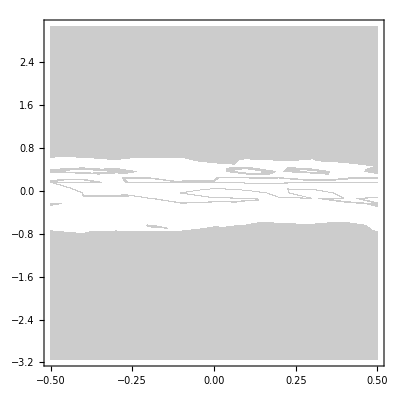

```mathematica
ListContourPlot[Flatten[Table[{δ,Δ,Fun[1,1,200,δ*10^6,Δ*10^9]},{δ,-0.5,0.5,0.1},{Δ,-2Pi 0.5,2Pi 0.5,0.1}],1]]
```

```mathematica
a1=ListPlot[
Table[
Im[Total[Solve[
M9[[{2,3,4,5,7,8,9,10,12,13,14,15},2]]==0/.{Subscript[σ, 1,1][t]->0,Subscript[σ, 2,2][t]->1,Subscript[σ, 3,3][t]->0,Subscript[σ, 4,4][t]->0,Δ1->i},{Subscript[σ, 1,2][t],Subscript[σ, 1,3][t],Subscript[σ, 1,4][t],Subscript[σ, 2,1][t],Subscript[σ, 2,3][t],Subscript[σ, 2,4][t],Subscript[σ, 3,1][t],Subscript[σ, 3,2][t],Subscript[σ, 3,4][t],Subscript[σ, 4,1][t],Subscript[σ, 4,2][t],Subscript[σ, 4,3][t]}][[1,{8,11},2]]]]

,{i,-5*10^9,5*10^9,0.01*10^9}],Joined->True,PlotRange->All,PlotLabel->"P_Coup= "<>ToString[1000P1]<>"mW P_Prob = "<>ToString[1000P2]<>"mW",Frame->True,Axes->False,ImageSize->Small
];
omegac1=1Ω13;
γ21=2Pi 1.4*10^6;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
δ=0;
a2=ListPlot[
Table[
Im[((4 √5 omegac1^2-5 √14 omegac1^2+16 ⅈ √5 γ32 δ-16 √5 δ^2-16 √5 δ Δ+16 √5 γ21 (γ32+ⅈ (δ+Δ))) Ω32)/(10 (-7 ⅈ omegac1^2 γ32-2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+2 w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))+((35 omegac1^2-2 √70 omegac1^2+40 ⅈ w43 (γ21+ⅈ δ)+40 ⅈ γ42 δ-40 δ^2-40 δ Δ+40 γ21 (γ42+ⅈ (δ+Δ))) Ω32)/(10 (-7 ⅈ omegac1^2 γ32-2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+2 w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))],{Δ,-5*10^9,5*10^9,0.01*10^9}],Joined->True,PlotRange->All,PlotStyle->{Red,Dashed}];
g1=Append[g1,Show[a1,a2]];
,{P1,0,0.05,0.0025},{P2,0.1/1000,1/1000,0.1/1000}]
```

## γ34≠0

```mathematica
testdata1=Flatten[Table[Transpose[Flatten[{{Table[δ,{i,1,Length[Range[-0.5,0.5,0.0005]]}]},Transpose[Lev3Testsc[30,200/1000,1/1000,0.5*10^6,δ*10^6,1,1,0,200]]},1]],{δ,Range[-700,500,1]}],1];
func=Interpolation[testdata1];
DensityPlot[func[x,y],{x,-700,500},{y,-0.5,0.5},ImageSize->800,PlotPoints->200,ClippingStyle->Automatic]
```

-Graphics-

## Hello

```mathematica
(d32^2 Nat (omegac1^2  β(α-β)))/(e0  (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ)+(d32^2 Nat omegac1^2 α (α-β))/(e0 (4 (γ21+ⅈ δ) (w43-ⅈ γ32+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43+(1+α^2) (-ⅈ γ32+δ+Δ))) ℏ)//ExpandAll//FullSimplify//ExpandAll//FullSimplify
```

(d32^2 Nat omegac1^2 (α-β) (4 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ)) (w43 (α+β)+β (-ⅈ γ32+δ+Δ)+α (-ⅈ γ42+δ+Δ))+omegac1^2 (w43 (α+β)+α^3 (-ⅈ γ32+δ+Δ)+β (-ⅈ γ32+δ+Δ)+α^2 β (-ⅈ γ32+δ+Δ)+α (-ⅈ γ42+δ+Δ))))/(e0 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) (4 (γ21+ⅈ δ) (w43-ⅈ γ32+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43+(1+α^2) (-ⅈ γ32+δ+Δ))) ℏ)

```mathematica
(4 β^2 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ42+δ+Δ+w43)-ⅈ β^2 omegac1^2) ℏ)+(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ)//ExpandAll//FullSimplify
```

-(8 d32^2 Nat (γ21+ⅈ δ) (-ⅈ omegac1^2 β^2+2 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ+β^2 (-ⅈ γ32+δ+Δ))))/(e0 (omegac1^2 β^2+4 ⅈ (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ)) (omegac1^2+4 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))) ℏ)

## Doppler

```mathematica
χ42=-(d32^2 Nat β (omegac1^2 (α-β)+4 β (-ⅈ γ21+δ) (-ⅈ γ32+δ+Δ)))/(e0 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ);   
χ32=(d32^2 Nat (omegac1^2 α (α-β)+4 ⅈ (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ)))/(e0 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))) ℏ);
```

```mathematica
s42=χ42/.Δ->Δ+wc v/c/.δ->δ;
s42=s42/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify//ExpandAll//Simplify;
s32=χ32/.Δ->Δ+wc v/c/.δ->δ;
s32=s32/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
```

```mathematica
Dopp[s42]//FullSimplify
Dopp[s32]
```

{-(ⅈ (4 ⅈ v^2 wc^2 (γ21+ⅈ δ)+c v wc (omegac1^2 (1+α^2)+4 (γ21+ⅈ δ) (ⅈ w43+γ32+γ42+2 ⅈ δ+2 ⅈ Δ))+c^2 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ)))))/(4 wc^2 (γ21+ⅈ δ)),(c (ⅈ omegac1^2 (α-β)+4 β (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)))/(4 wc β (γ21+ⅈ δ)),(c d32^2 Nat β^2)/(e0 √π u wc ℏ)}

{-(ⅈ (4 ⅈ v^2 wc^2 (γ21+ⅈ δ)+c v wc (omegac1^2 (1+α^2)+4 (γ21+ⅈ δ) (ⅈ w43+γ32+γ42+2 ⅈ (δ+Δ)))+c^2 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ)))))/(4 wc^2 (γ21+ⅈ δ)),(c (-ⅈ omegac1^2 α (α-β)+4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ)))/(4 wc (γ21+ⅈ δ)),(c d32^2 Nat)/(e0 √π u wc ℏ)}

```mathematica
CoefficientList[-(ⅈ (4 ⅈ v^2 wc^2 (γ21+ⅈ δ)+c v wc (omegac1^2 (1+α^2)+4 (γ21+ⅈ δ) (ⅈ w43+γ32+γ42+2 ⅈ δ+2 ⅈ Δ))+c^2 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ)))))/(4 wc^2 (γ21+ⅈ δ)),v]//FullSimplify
```

{-(ⅈ c^2 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))))/(4 wc^2 (γ21+ⅈ δ)),-(ⅈ c (omegac1^2 (1+α^2)+4 (γ21+ⅈ δ) (ⅈ w43+γ32+γ42+2 ⅈ (δ+Δ))))/(4 wc (γ21+ⅈ δ)),1}

```mathematica
(c omegac1^2 (1+α^2))/(4 wc (ⅈ γ21- δ))+c/wc ( w43-ⅈ γ32-ⅈ γ42+2 (δ+Δ))//Together
```

```mathematica
(c (-ⅈ omegac1^2-ⅈ omegac1^2 α^2+4 w43 γ21-4 ⅈ γ21 γ32-4 ⅈ γ21 γ42+4 ⅈ w43 δ+8 γ21 δ+4 γ32 δ+4 γ42 δ+8 ⅈ δ^2+8 γ21 Δ+8 ⅈ δ Δ))/(4 wc (γ21+ⅈ δ))//FullSimplify
```

-(ⅈ c (omegac1^2 (1+α^2)+4 (γ21+ⅈ δ) (ⅈ w43+γ32+γ42+2 ⅈ (δ+Δ))))/(4 wc (γ21+ⅈ δ))

```mathematica
c^2/wc^2(w43-ⅈ γ42+δ+Δ) (-ⅈ γ32+(δ+Δ))+(c^2 omegac1^2)/(4 wc^2 (ⅈ γ21- δ)) (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))//Together//FullSimplify
```

-(ⅈ c^2 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ))))/(4 wc^2 (γ21+ⅈ δ))

```mathematica
-(ⅈ (4 ⅈ v^2 wc^2 (γ21+ⅈ δ)+c v wc (omegac1^2 (1+α^2)+4 (γ21+ⅈ δ) (ⅈ w43+γ32+γ42+2 ⅈ δ+2 ⅈ Δ))+c^2 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ)))))/(4 wc^2 (γ21+ⅈ δ))//FullSimplify
```

-(ⅈ (4 ⅈ v^2 wc^2 (γ21+ⅈ δ)+c v wc (omegac1^2 (1+α^2)+4 (γ21+ⅈ δ) (ⅈ w43+γ32+γ42+2 ⅈ (δ+Δ)))+c^2 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ)))))/(4 wc^2 (γ21+ⅈ δ))

```mathematica
Solve[-(ⅈ (4 ⅈ v^2 wc^2 (γ21+ⅈ δ)+c v wc (omegac1^2 (1+α^2)+4 (γ21+ⅈ δ) (ⅈ w43+γ32+γ42+2 ⅈ δ+2 ⅈ Δ))+c^2 (4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))+omegac1^2 (w43-ⅈ γ42+δ+Δ+α^2 (-ⅈ γ32+δ+Δ)))))/(4 wc^2 (γ21+ⅈ δ))==0,v]//FullSimplify
```

{{v→-(√(-c^2 wc^2 (omegac1^2 (-ⅈ+α)^2+4 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ)) (omegac1^2 (ⅈ+α)^2+4 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ)))-ⅈ c wc (omegac1^2 (1+α^2)+4 (γ21+ⅈ δ) (ⅈ w43+γ32+γ42+2 ⅈ (δ+Δ))))/(8 wc^2 (γ21+ⅈ δ))},{v→(√(-c^2 wc^2 (omegac1^2 (-ⅈ+α)^2+4 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ)) (omegac1^2 (ⅈ+α)^2+4 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ)))+ⅈ c wc (omegac1^2 (1+α^2)+4 (γ21+ⅈ δ) (ⅈ w43+γ32+γ42+2 ⅈ (δ+Δ))))/(8 wc^2 (γ21+ⅈ δ))}}